# CRSISF fitting

### data loading

```mathematica
p0s={3.85,3.825,3.80,3.75};
```

```mathematica
temperatures={{0.039 ,0.016, 0.01 ,0.005 ,0.00385, 0.0025 ,0.002, 0.001 ,0.0005 ,0.00033 ,0.00025, 0.00014, 0.000091,0.000077,0.000054, 0.000045, 0.000036},{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022},{0.063, 0.039, 0.03105, 0.025 ,0.02, 0.016, 0.014,0.012 ,0.011, 0.01, 0.0093}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{ 999999, 999999, 999999,999999, 999999,60, 80, 200, 500, 800, 999999, 999999, 999999,999999, 999999, 999999, 999999},{ 999999, 999999, 999999,999999, 999999,25, 40 ,60, 80, 120,200 ,300 ,1000 ,999999, 999999,999999},{ 999999, 999999, 999999,999999, 999999,40 ,70 ,150 ,250, 600 ,2000, 999999 ,999999, 999999},{ 999999, 999999, 999999,10 ,30 ,70, 150 ,700,1400, 999999 ,999999}};
```

```mathematica
CRSISF=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/timeCRSISF_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],Floor[If[tauEstimate[[p,T]]==999999,tauEstimate[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10]]
],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
fitStartPos=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
fitEndPos=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
betaConstraints=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
plateauConstraints=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
tauConstraints=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
fittings=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
initialPlateau=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
initialBeta=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
initialTau=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
betaResults=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
tauAlphaResults=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
plateauResults=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
numExp=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
noiseLevel=Table[Table[{},{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

## Final results

### fitting results

```mathematica
fittings
```

{{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}},{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}},{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}},{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}}

```mathematica
fittings={{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}},{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}},{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}},{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}};
```

### fitting parameters

```mathematica
tauOldfitting={{1.42.6,4.71.5,8.91.7,20.91.5,28.01.5,48.4.,74.63.0,193.4.,557.10.,1213.42.,1624.29.,4184.45.,10376.187.,11687.237.,25941.343.,31903.490.,44031.615.},{1.24.,2.4.,3.22.8,9.01.5,18.51.6,27.5.,41.5.,56.4.,95.5.,136.6.,227.11.,303.8.,563.9.,1171.15.,4893.45.,13252.74.},{1.13.,2.12.,3.7.,5.24.,11.02.2,34.6.,58.10.,113.11.,234.7.,586.14.,1595.24.,2672.20.,4596.20.,8808.36.},{1.42.3,3.52.6,6.22.0,11.92.0,23.71.6,65.5.,170.4.,693.11.,1497.9.,4466.59.,11419.141.}};
```

```mathematica
tauAlphaResults=Table[Table[Around[Mean[Table[fittings[[p,T,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[p,T]]]}]],StandardDeviation[Table[fittings[[p,T,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[p,T]]]}]]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
plateauResults=Table[Table[Around[Mean[Table[fittings[[p,T,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[p,T]]]}]],StandardDeviation[Table[fittings[[p,T,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[p,T]]]}]]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
betaResults=Table[Table[Around[Mean[Table[fittings[[p,T,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[p,T]]]}]],StandardDeviation[Table[fittings[[p,T,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[p,T]]]}]]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];;
```

```mathematica
tauAlphaResults
```

{{1.1830.014,5.60.6,8.91.1,23.4.,33.4.,52.4.,70.8.,185.19.,470.41.,929.84.,1389.113.,3734.449.,7188.896.,9930.697.,2.040.1810^4,2.90.410^4,4.10.510^4},{0.7900.028,2.290.33,3.00.5,8.20.6,18.61.7,26.72.3,38.92.7,53.81.7,86.8.,117.10.,170.24.,250.27.,478.55.,1166.99.,4460.663.,1.300.2810^4},{0.8120.017,2.760.25,3.930.30,5.50.5,13.31.6,39.4.,62.9.,114.14.,225.35.,550.46.,1423.279.,2572.497.,4591.765.,8.31.210^3},{1.930.30,4.30.4,8.20.9,13.31.8,25.7.,65.6.,175.19.,622.137.,1311.198.,4.71.510^3,1.070.2110^4}}

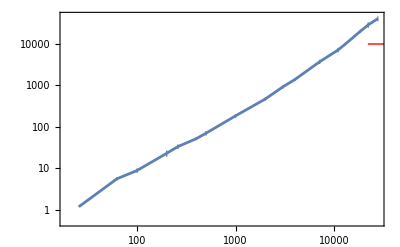
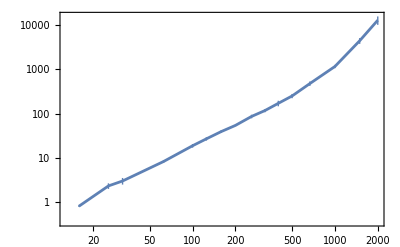
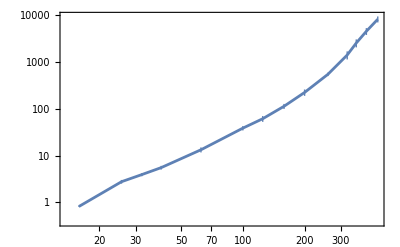

```mathematica
Table[Show[ListLogLogPlot[{Table[{1/temperatures[[p,T]],tauAlphaResults[[p,T]]},{T,Length[temperatures[[p]]]}]},Joined->True,PlotRange->All,ImageSize->400],LogPlot[10000,{x,10,50000},PlotStyle->{Thin,Red}]],{p,Length[p0s]}]
```

```mathematica
tg=1/{13344.874052727082,1889.5184135977338,473.33734176303693,107.42605591909576}
```

{0.0000749351,0.000529235,0.00211266,0.00930873}

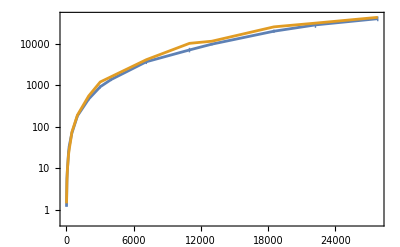
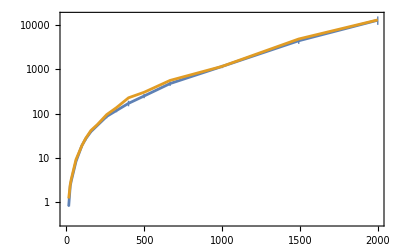
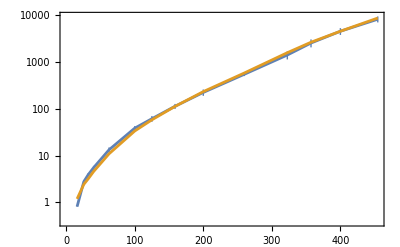
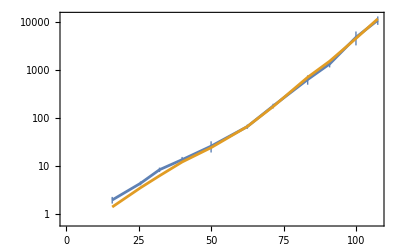

```mathematica
Table[ListLogPlot[{Table[{1/temperatures[[p,T]],tauAlphaResults[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{1/temperatures[[p,T]],tauOldfitting[[p,T,1]]},{T,Length[temperatures[[p]]]}]},Joined->True],{p,Length[p0s]}]
```

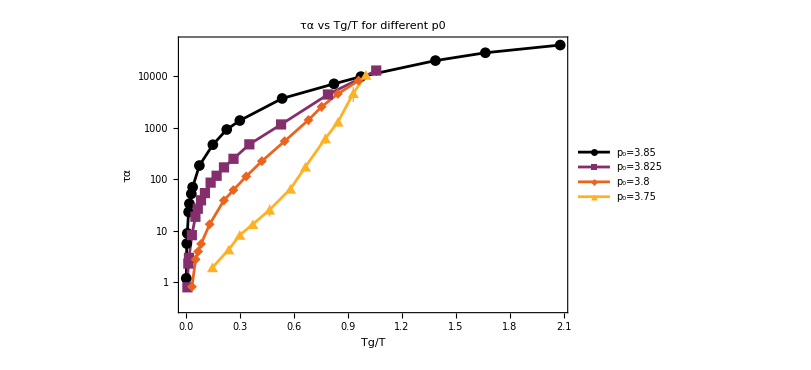

```mathematica
tauAlphaPlot=Show[ListLogPlot[Table[Table[{tg[[p]]/temperatures[[p,T]],tauAlphaResults[[p,T]]},{T,Length[temperatures[[p]]]}],{p,1,4}],PlotStyle->gradientColScheme[5],PlotMarkers->Automatic,FrameLabel->{"Tg/T","τα"},PlotRange->All,Joined->True,ImageSize->600,PlotLabel->"τα vs Tg/T for different p0", PlotLegends->Table["p_0="<>ToString[p0s[[p]]],{p,4}]]]
```

```mathematica
Export["/home/chengling/Research/updates/07282024/tauAlphaPlot.jpeg",tauAlphaPlot,ImageResolution->300]
```

/home/chengling/Research/updates/07282024/tauAlphaPlot.jpeg

```mathematica
tauAlphaTable=Table[Prepend[Table[Flatten[{temperatures[[p,T]],tauAlphaResults[[p,T,1]],tauAlphaResults[[p,T,2]],Table[fittings[[p,T,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[p,T]]]}]}],{T,Length[temperatures[[p]]]}],Flatten[{"T","TraditionalForm`Mean","StandardDeviation",Table["configuration "<>ToString[i],{i,10}]}]],{p,Length[p0s]}]
```

{{{T,TraditionalForm`Mean,StandardDeviation,configuration 1,configuration 2,configuration 3,configuration 4,configuration 5,configuration 6,configuration 7,configuration 8,configuration 9,configuration 10},{0.039,1.1833,0.0141384,1.16082,1.16354,1.18378,1.202,1.1973,1.19818,1.18625,1.18859,1.17558,1.17699},{0.016,5.59894,0.5617,6.02715,5.22126,6.60654,5.37571,5.39535,5.67817,5.20164,6.39254,5.06295,5.02815},{0.01,8.86968,1.07987,7.53372,7.92773,7.98507,8.63708,9.54208,10.9703,8.88343,8.20377,10.1648,8.84876},{0.005,23.0692,3.7912,20.3693,23.7211,20.0716,27.3103,17.761,19.4686,26.7243,24.6746,29.0158,21.5749},{0.00385,33.4722,4.30552,25.4657,37.7611,30.5531,28.689,30.8838,36.28,36.241,37.8125,36.8372,34.1982},{0.0025,52.136,4.28084,49.4781,51.607,53.5683,45.457,58.1537,50.1471,57.2416,46.4648,54.3279,54.9149},{0.002,70.2611,8.34002,56.4377,70.2617,73.1253,70.5943,67.6436,59.091,68.0783,85.0929,76.8628,75.4234},{0.001,184.839,18.986,166.42,159.818,197.63,185.105,168.862,162.699,196.745,194.035,211.715,205.361},{0.0005,469.997,41.3596,405.781,437.133,519.264,521.297,444.583,467.824,489.93,425.882,516.197,472.076},{0.00033,928.914,83.98,1034.26,786.89,972.106,1004.97,930.126,907.632,874.586,914.85,829.551,1034.17},{0.00025,1388.86,112.6,1329.81,1325.91,1447.83,1432.13,1552.63,1349.7,1190.1,1297.36,1544.37,1418.72},{0.00014,3733.8,448.753,4156.12,3012.68,3170.68,3579.4,3936.87,4136.76,3995.64,4036.62,3210.9,4102.3},{0.000091,7188.02,895.875,6682.72,7866.,8081.01,6494.88,7402.28,7983.26,8248.3,6292.29,7260.24,5569.24},{0.000077,9930.44,696.928,9937.31,10544.,9692.7,10878.,10838.5,9788.05,10276.1,9357.48,9026.55,8965.67},{0.000054,20363.4,1847.31,19653.1,18977.9,18331.9,22315.8,18297.8,22373.7,22739.2,22117.7,20283.9,18543.},{0.000045,28926.2,4308.79,25605.4,29796.9,35150.7,23926.1,22410.6,29489.4,32749.7,33173.3,31284.8,25675.1},{0.000036,40853.7,5364.19,39389.,49972.2,36446.5,38761.3,36628.,48253.7,33453.9,38772.,44994.5,41865.5}},{{T,TraditionalForm`Mean,StandardDeviation,configuration 1,configuration 2,configuration 3,configuration 4,configuration 5,configuration 6,configuration 7,configuration 8,configuration 9,configuration 10},{0.063,0.790033,0.0279207,0.793032,0.790489,0.775013,0.757066,0.751017,0.814992,0.791936,0.825984,0.832323,0.768475},{0.039,2.28957,0.330786,2.3498,2.44038,2.30105,1.76619,1.93793,2.2706,2.69929,2.65397,1.88161,2.59493},{0.03105,2.95825,0.504713,2.31033,3.00386,2.39348,3.38551,3.32798,3.22229,2.46589,3.52741,3.51878,2.42698},{0.016,8.17517,0.557373,7.22142,7.86412,8.35744,8.83946,8.2567,7.29953,8.67808,8.14497,8.46033,8.62966},{0.01,18.6243,1.73212,17.9652,20.9706,17.3871,16.8658,17.4781,20.3056,16.5587,18.7798,18.4813,21.4506},{0.008,26.7057,2.3018,25.1554,26.5198,24.8628,25.3739,25.0729,31.5526,25.9947,30.185,25.5648,26.7751},{0.0063,38.9326,2.69104,39.051,37.0528,42.5083,42.2121,38.73,35.6131,38.8573,42.5882,36.7962,35.9171},{0.005,53.8266,1.69311,53.1653,55.3309,54.0013,56.6053,55.589,51.6224,51.6573,52.5935,53.0904,54.6109},{0.00385,85.9895,7.89394,80.7383,73.8862,85.4155,80.9037,100.993,82.0944,91.403,81.0739,92.6287,90.7583},{0.0031,116.961,9.78409,109.99,114.503,107.809,124.949,125.164,121.242,128.092,108.287,128.3,101.275},{0.0025,170.269,24.3522,179.18,202.686,161.483,152.401,144.405,208.2,137.989,183.955,151.357,181.033},{0.002,249.988,27.4442,282.376,270.164,240.025,191.477,251.524,232.816,269.368,263.207,227.645,271.274},{0.0015,477.786,54.5814,492.932,450.055,509.825,455.909,455.794,454.194,582.238,521.996,375.797,479.116},{0.001,1165.83,98.5864,1270.57,1265.52,1123.16,1185.55,1089.03,1288.13,1218.55,1056.59,996.165,1165.01},{0.00067,4460.35,662.557,4041.8,4077.29,4459.95,4759.57,4576.19,5499.9,3799.15,4389.69,5499.99,3500.01},{0.0005,13046.3,2809.36,15300.5,10788.3,9323.98,13261.9,12968.2,15128.8,11629.6,18720.8,13189.,10151.5}},{{T,TraditionalForm`Mean,StandardDeviation,configuration 1,configuration 2,configuration 3,configuration 4,configuration 5,configuration 6,configuration 7,configuration 8,configuration 9,configuration 10},{0.063,0.812359,0.017292,0.80086,0.798091,0.792575,0.816617,0.823598,0.793925,0.808113,0.819445,0.821588,0.848777},{0.039,2.76481,0.24901,2.86841,2.67888,2.26229,2.75284,2.45638,2.77583,2.95268,3.06805,3.0134,2.81932},{0.03105,3.92695,0.30309,4.05079,3.7343,4.24275,4.11566,3.9403,3.78714,3.18954,4.02725,4.01448,4.16728},{0.025,5.53225,0.497122,5.65312,6.2107,5.69378,5.91496,5.36755,5.52508,4.60823,5.44272,4.87213,6.03418},{0.016,13.3267,1.63435,10.3804,15.0829,14.6202,12.1786,13.8625,15.8662,12.4525,13.8849,12.4334,12.5059},{0.01,38.707,4.10903,31.14,43.0099,34.1383,41.1859,39.9446,40.3674,35.8011,42.4467,36.2677,42.7685},{0.008,61.5755,8.71697,64.1912,63.0843,56.4488,56.5898,61.1332,55.3384,60.7382,61.2782,52.8481,84.1045},{0.0063,113.702,13.9355,102.636,128.176,112.149,108.726,88.664,129.419,122.858,99.0334,117.454,127.902},{0.005,225.111,34.9366,191.657,194.119,221.281,244.567,198.412,221.268,216.414,245.559,308.942,208.888},{0.00385,550.157,45.8509,550.172,532.959,512.017,608.635,520.313,518.11,556.325,590.286,485.29,627.467},{0.0031,1423.11,278.959,1390.21,1179.52,1658.19,1656.9,1649.64,1085.5,1362.38,1468.26,967.857,1812.66},{0.0028,2571.7,497.221,1840.31,2931.34,2883.58,2345.57,3190.,2758.57,2292.85,2331.02,1916.35,3227.45},{0.0025,4591.21,764.961,3864.04,4766.53,5090.13,4583.4,5073.75,4963.5,6036.,4280.38,3479.28,3775.04},{0.0022,8306.58,1211.97,9440.23,8455.99,7496.64,6940.83,6495.22,9857.81,7310.42,9443.85,8139.25,9485.59}},{{T,TraditionalForm`Mean,StandardDeviation,configuration 1,configuration 2,configuration 3,configuration 4,configuration 5,configuration 6,configuration 7,configuration 8,configuration 9,configuration 10},{0.063,1.92629,0.304479,1.73903,2.25265,1.50522,2.02124,2.16412,2.20385,2.00497,1.42329,1.74074,2.2078},{0.039,4.28754,0.385223,3.93425,4.36442,3.89567,4.1742,4.45253,4.1118,4.63237,3.8654,4.33187,5.11292},{0.03105,8.2299,0.870566,8.66153,8.69725,7.06172,7.92001,7.8435,9.26457,7.06425,8.09225,9.74042,7.95354},{0.025,13.3234,1.84979,14.7879,14.2608,15.7008,13.8567,13.68,13.2937,10.4577,15.0652,10.6998,11.4316},{0.02,25.4613,6.67421,20.8707,33.268,16.3588,16.6402,30.985,27.9242,18.2839,28.2634,30.4113,31.6073},{0.016,65.0525,6.38444,62.8449,73.6809,57.8897,69.5328,72.3414,70.306,56.3544,59.6555,67.7179,60.2015},{0.014,175.206,19.4643,148.507,171.475,157.363,198.609,212.758,170.578,186.64,164.63,177.929,163.575},{0.012,622.303,136.864,773.949,414.329,725.584,608.992,496.054,527.329,609.034,767.406,502.278,798.075},{0.011,1311.41,198.437,1506.14,1274.35,1459.17,1443.76,1360.,1047.63,1001.12,1592.88,1283.53,1145.47},{0.01,4715.68,1515.91,4497.3,2832.32,6626.76,3386.37,5442.21,4553.6,4083.79,5968.89,2751.11,7014.45},{0.0093,10694.5,2124.07,9044.44,12589.9,12742.3,9528.82,11420.2,13541.4,10094.5,9773.65,6473.87,11735.7}}}

```mathematica
Table[Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP"<>ToString[NumberForm[p0s[[p]],{5,3}]]<>".csv",tauAlphaTable[[p]],"CSV"],{p,Length[p0s]}]
```

{/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP3.850.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP3.825.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP3.800.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP3.750.csv}

## p_0=3.85

### T=0.000036

```mathematica
curP=1;curT=17;
```

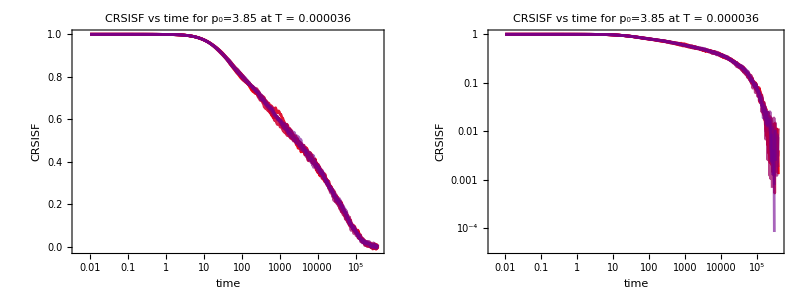

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,300,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.0153629,0.0162528,0.0154672,0.0159807,0.0160517,0.0155748,0.017756,0.01544,0.0167026,0.0157377}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>10000&)][[1,1]],{i,10}]
```

{481,481,481,481,481,481,481,481,481,481}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(#<0.5*10^-2&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{614,612,620,625,619,619,610,619,621,618}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.6;
initialTau[[curP,curT]]=40000.;
betaConstraints[[curP,curT]]=1.0>β>0.5;
plateauConstraints[[curP,curT]]=0.55>G>0.45;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT]],plateauConstraints[[curP,curT]],50000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.528949,0.451794,0.54993,0.546834,0.549996,0.479429,0.549942,0.533578,0.495375,0.513587}

0.5200.034

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{39389.,49972.2,36446.5,38761.3,36628.,48253.7,33453.9,38772.,44994.5,41865.5}

4.10.510^4

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.773307,0.869173,0.681971,0.753579,0.707994,0.832095,0.724781,0.735435,0.801997,0.776494}

0.770.06

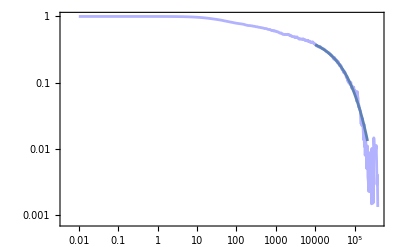
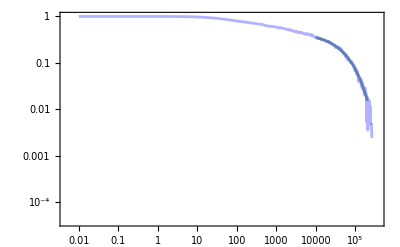
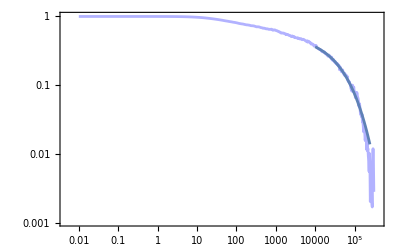
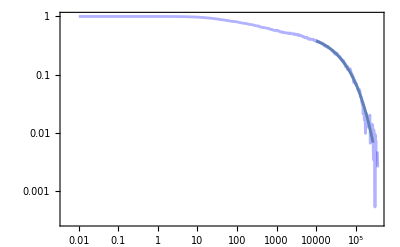
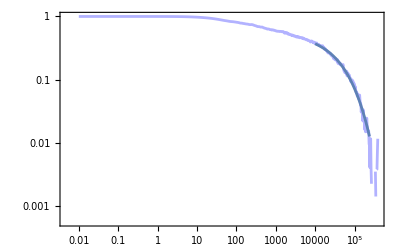
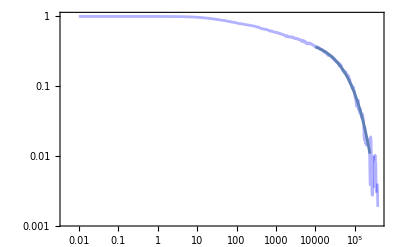
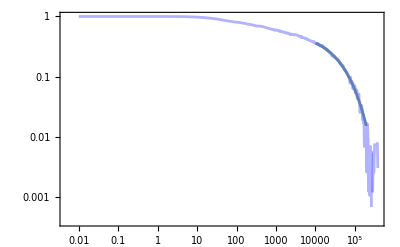
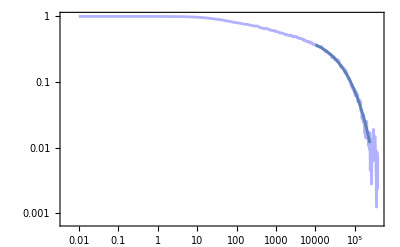

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,fitEndPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

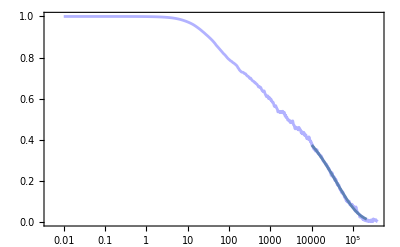
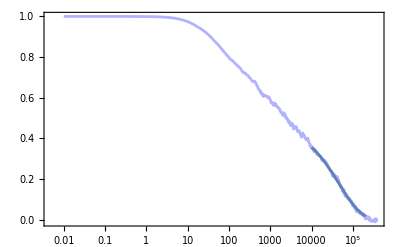
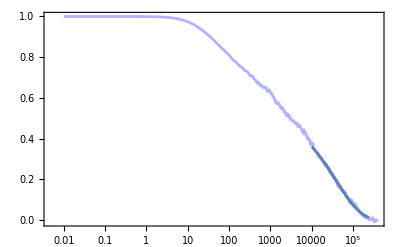
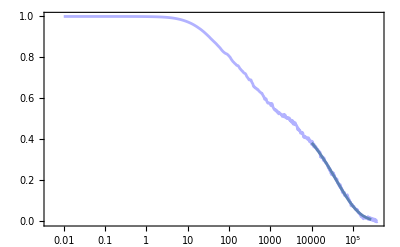
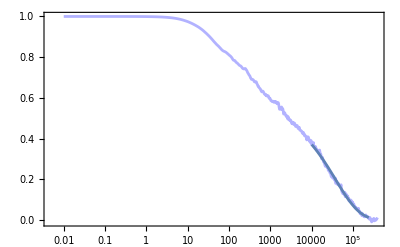
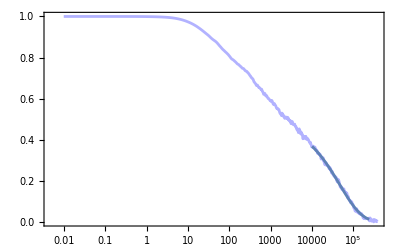
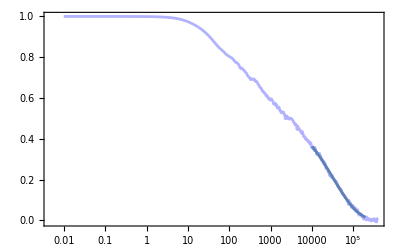
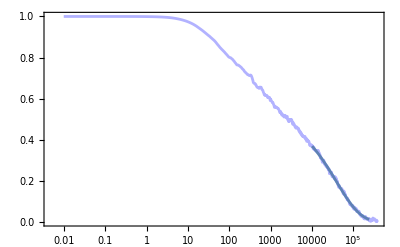

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,fitEndPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.000045

```mathematica
curP=1;curT=16;
```

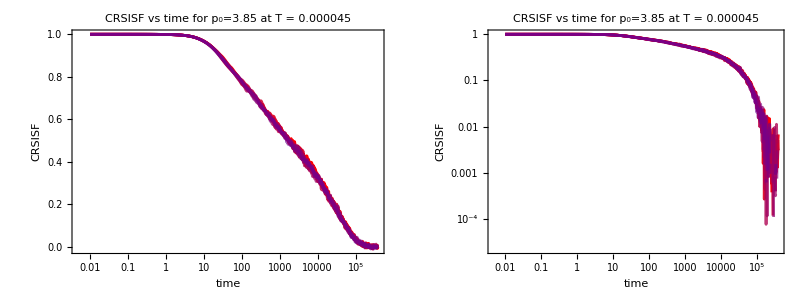

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>8000&)][[1,1]],{i,10}]
```

{472,472,472,472,472,472,472,472,472,472}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(#<1*10^-2&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{602,597,593,598,592,593,591,602,596,598}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{640,640,640,640,640,639,639,639,638,639}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.6;
initialTau[[curP,curT]]=30000.;
betaConstraints[[curP,curT]]={1.0>β>0.5,0.99>β>0.60,0.99>β>0.60,0.99>β>0.60,0.99>β>0.60,0.99>β>0.60,0.99>β>0.60,0.99>β>0.60,0.99>β>0.60,0.99>β>0.60};
plateauConstraints[[curP,curT]]=0.9>G>0.45;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT]],plateauConstraints[[curP,curT]],50000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.568968,0.490478,0.450005,0.558075,0.567071,0.489063,0.450005,0.463678,0.47889,0.53148}

0.500.05

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{25605.4,29796.9,35150.7,23926.1,22410.6,29489.4,32749.7,33173.3,31284.8,25675.1}

2.90.410^4

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.702155,0.801599,0.85442,0.705969,0.679491,0.77785,0.846833,0.856162,0.834167,0.744935}

0.780.07

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,fitEndPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,fitEndPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.000054

```mathematica
curP=1;curT=15;
```

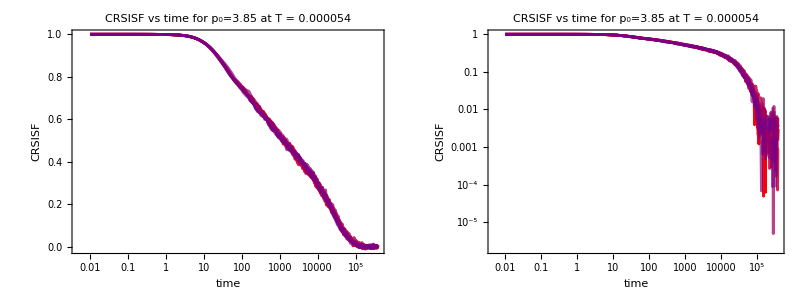

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,600,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.0128961,0.0121312,0.0110028,0.0102223,0.0108405,0.0136015,0.012661,0.0127486,0.013525,0.0115322}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>2000&)][[1,1]],{i,10}]
```

{412,412,412,412,412,412,412,412,412,412}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(#<noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{573,582,580,579,596,579,578,574,581,574}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.7;
initialTau[[curP,curT]]=20000.;
betaConstraints[[curP,curT]]=1.0>β>0.3;
plateauConstraints[[curP,curT]]=0.9>G>0.5;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT]],plateauConstraints[[curP,curT]],50000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.531645,0.544358,0.542219,0.500003,0.557852,0.526384,0.505575,0.522122,0.511874,0.544972}

```mathematica
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],
StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

0.5290.019

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],
StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{19653.1,18977.9,18331.9,22315.8,18297.8,22373.7,22739.2,22117.7,20283.9,18543.}

2.040.1810^4

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],
StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.773708,0.750855,0.684707,0.848706,0.685921,0.740186,0.765119,0.816562,0.824071,0.768884}

0.770.05

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,fitEndPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],200000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.000077

```mathematica
curP=1;curT=14;
```

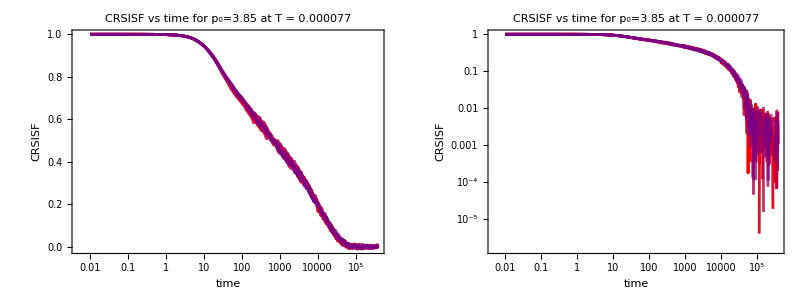

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,600,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.0102114,0.00958092,0.0112001,0.00978779,0.0102498,0.011214,0.0107019,0.0113317,0.00989071,0.0105902}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>2000&)][[1,1]],{i,10}]
```

{412,412,412,412,412,412,412,412,412,412}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(#<noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{551,556,560,544,544,558,550,550,559,551}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.7;
initialTau[[curP,curT]]=10000.;
betaConstraints[[curP,curT]]=1.0>β>0.1;
plateauConstraints[[curP,curT]]=0.9>G>0.5;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT]],plateauConstraints[[curP,curT]],50000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.533875,0.50003,0.557493,0.51205,0.500003,0.54262,0.519224,0.57258,0.568895,0.556095}

0.5360.027

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{9937.31,10544.,9692.7,10878.,10838.5,9788.05,10276.1,9357.48,9026.55,8965.67}

9930.697.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.777302,0.772756,0.692958,0.827972,0.751564,0.741258,0.720988,0.704027,0.639369,0.67008}

0.730.06

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,fitEndPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],200000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.000091

```mathematica
curP=1;curT=13;
```

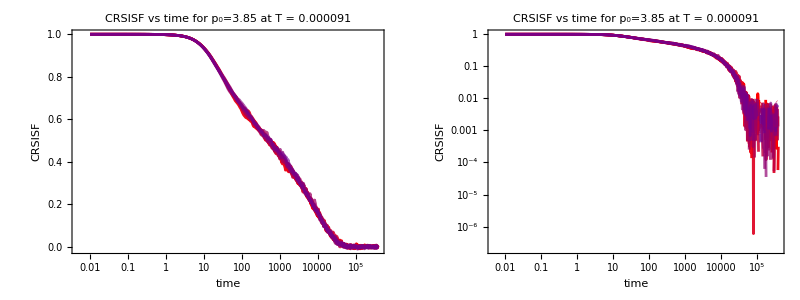

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,590,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.0106692,0.0101706,0.0103434,0.0104623,0.00976815,0.0104649,0.0104912,0.00943213,0.0100462,0.0108924}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>1000&)][[1,1]],{i,10}]
```

{382,382,382,382,382,382,382,382,382,382}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(#<noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{546,546,543,544,537,532,548,539,546,536}

```mathematica
initialPlateau[[curP,curT]]=0.6;
initialBeta[[curP,curT]]=0.7;
initialTau[[curP,curT]]=6000.;
betaConstraints[[curP,curT]]=1.0>β>0.1;
plateauConstraints[[curP,curT]]=0.65>G>0.52;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT]],plateauConstraints[[curP,curT]],50000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],
StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.553296,0.520002,0.520005,0.590402,0.526991,0.520256,0.520002,0.589747,0.549429,0.640019}

0.550.04

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],
StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{6682.72,7866.,8081.01,6494.88,7402.28,7983.26,8248.3,6292.29,7260.24,5569.24}

7188.896.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],
StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.683152,0.70065,0.727488,0.605215,0.734478,0.746419,0.741142,0.680305,0.716788,0.608409}

0.690.05

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],300000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],200000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.00014

```mathematica
curP=1;curT=12;
```

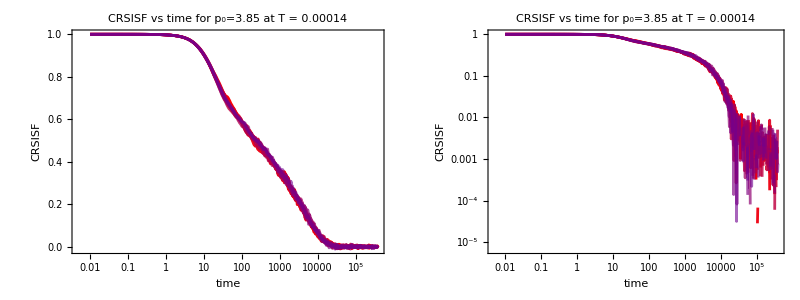

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,550,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.00972765,0.00959075,0.010091,0.010054,0.00860388,0.00954698,0.00987515,0.00972275,0.00844724,0.0100329}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>600&)][[1,1]],{i,10}]
```

{359,359,359,359,359,359,359,359,359,359}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(#<noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{506,509,513,511,508,518,514,503,507,512}

```mathematica
initialPlateau[[curP,curT]]=0.6;
initialBeta[[curP,curT]]=0.7;
initialTau[[curP,curT]]=4000.;
betaConstraints[[curP,curT]]=1.0>β>0.3;
plateauConstraints[[curP,curT]]=0.55>G>0.49;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT]],plateauConstraints[[curP,curT]],50000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],
StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.490006,0.549699,0.549965,0.529774,0.492235,0.492761,0.517159,0.514689,0.549993,0.507363}

0.5190.024

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],
StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{4156.12,3012.68,3170.68,3579.4,3936.87,4136.76,3995.64,4036.62,3210.9,4102.3}

3734.449.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],
StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.849216,0.684849,0.667487,0.712008,0.776486,0.769068,0.715952,0.752073,0.702573,0.815181}

0.740.06

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],50000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],50000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.00025

```mathematica
curP=1;curT=11;
```

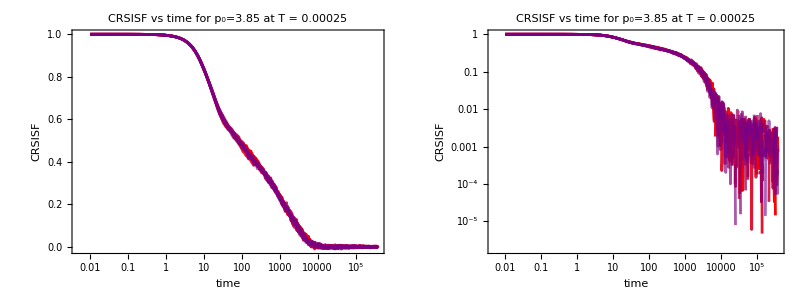

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,500,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.00813365,0.00954749,0.00847095,0.0084267,0.0078232,0.00837117,0.0088489,0.0088833,0.00842966,0.00858616}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>200&)][[1,1]],{i,10}]
```

{312,312,312,312,312,312,312,312,312,312}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(#<noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{473,459,472,465,467,467,473,463,466,477}

```mathematica
initialPlateau[[curP,curT]]=0.6;
initialBeta[[curP,curT]]=0.7;
initialTau[[curP,curT]]=1000.;
betaConstraints[[curP,curT]]=1.0>β>0.1;
plateauConstraints[[curP,curT]]=0.55>G>0.1
```

0.55>G>0.1

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT]],plateauConstraints[[curP,curT]],50000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],
StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.549997,0.513583,0.490797,0.510911,0.500317,0.520947,0.547366,0.534443,0.478039,0.513455}

0.5160.023

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],
StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{1329.81,1325.91,1447.83,1432.13,1552.63,1349.7,1190.1,1297.36,1544.37,1418.72}

1389.113.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],
StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.668934,0.778322,0.760532,0.777763,0.757652,0.716248,0.72058,0.696087,0.824651,0.713193}

0.740.05

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],50000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],50000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.00033

```mathematica
curP=1;curT=10;
```

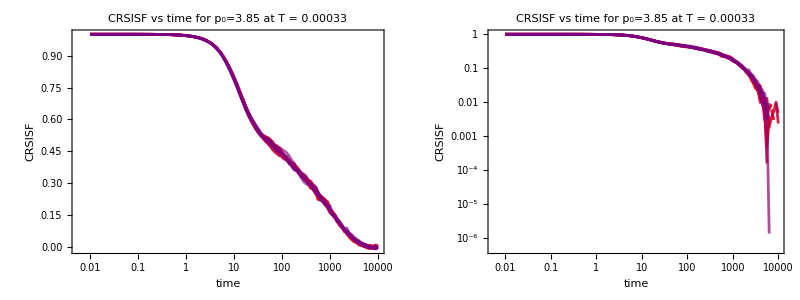

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,110,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.00149632,0.0127747,0.0155887,0.0161013,0.0019598,0.0099071,0.0159042,0.0013709,0.0064102,0.0155411}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>150&)][[1,1]],{i,10}]
```

{75,75,75,75,75,75,75,75,75,75}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(#<noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{108,104,102,104,105,104,103,106,106,104}

```mathematica
initialPlateau[[curP,curT]]=0.6;
initialBeta[[curP,curT]]=0.7;
initialTau[[curP,curT]]=4000.;
betaConstraints[[curP,curT]]=1.0>β>0.3;
plateauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT]],plateauConstraints[[curP,curT]],50000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],
StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.475665,0.540747,0.47778,0.483044,0.490441,0.502069,0.509171,0.49774,0.541332,0.471734}

0.4990.025

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],
StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{1034.26,786.89,972.106,1004.97,930.126,907.632,874.586,914.85,829.551,1034.17}

929.84.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],
StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.861833,0.683327,0.793761,0.803447,0.774902,0.736008,0.762457,0.757446,0.719458,0.744021}

0.760.05

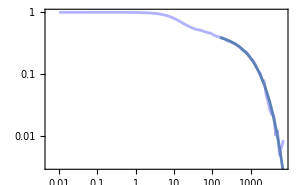
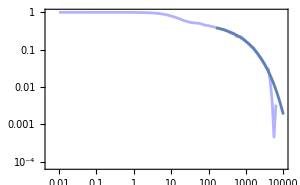
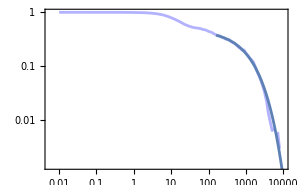
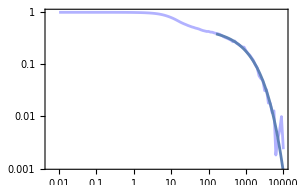
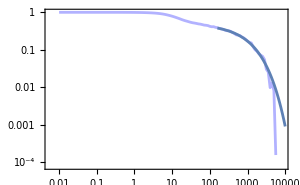
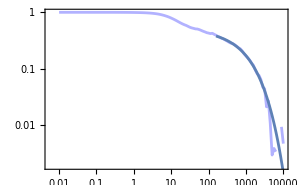
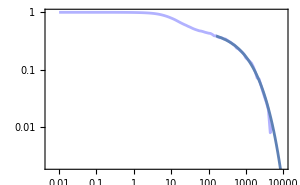
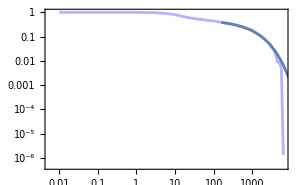

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True,ImageSize->300],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],10000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

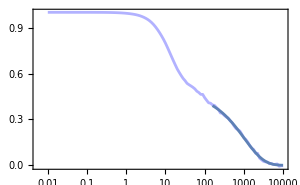
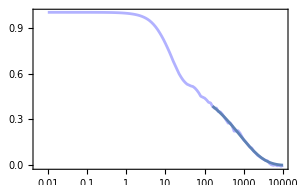
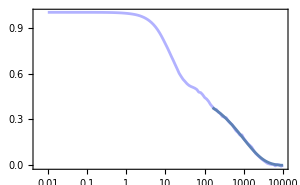
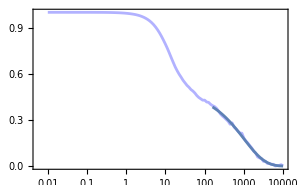
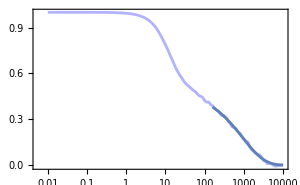
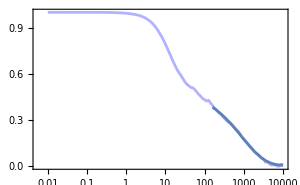
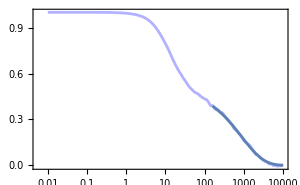
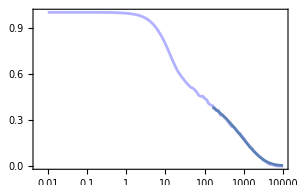

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True,ImageSize->300],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],10000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.0005

```mathematica
curP=1;curT=9;
```

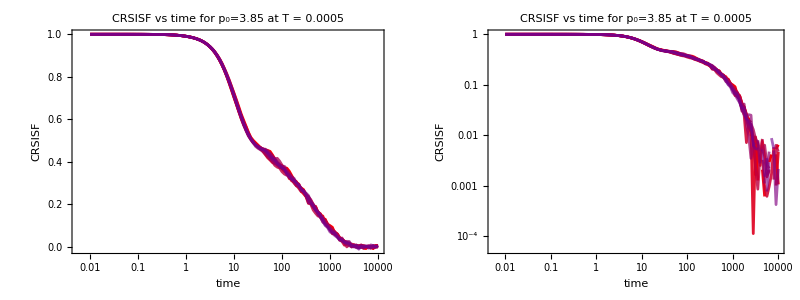

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>100&)][[1,1]],{i,10}]
```

{71,71,71,71,71,71,71,71,71,71}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,105,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.0210492,0.00793474,0.0106963,0.00773811,0.0143381,0.011044,0.00698356,0.00941899,0.0130456,0.0151178}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(#<noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{98,100,99,96,97,100,98,99,98,99}

```mathematica
initialPlateau[[curP,curT]]=0.6;
initialBeta[[curP,curT]]=0.7;
initialTau[[curP,curT]]=4000.;
betaConstraints[[curP,curT]]=1.0>β>0.3;
plateauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT]],plateauConstraints[[curP,curT]],50000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],
StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.571634,0.525033,0.471854,0.476571,0.509827,0.506995,0.488116,0.54707,0.466328,0.493342}

0.5060.034

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],
StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{405.781,437.133,519.264,521.297,444.583,467.824,489.93,425.882,516.197,472.076}

470.41.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],
StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.664631,0.697773,0.827044,0.795538,0.706759,0.742798,0.806212,0.707657,0.882808,0.787071}

0.760.07

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],10000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],10000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.001

```mathematica
curP=1;curT=8;
```

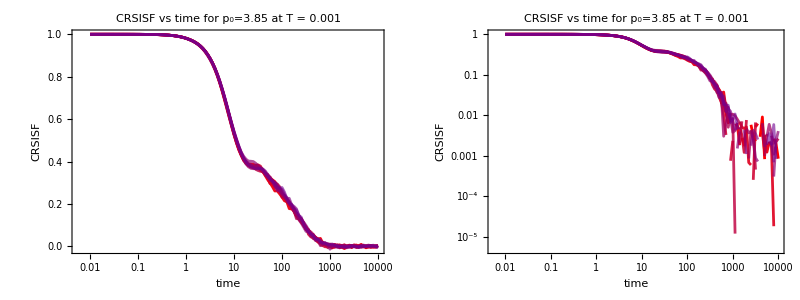

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>50&)][[1,1]],{i,10}]
```

{65,65,65,65,65,65,65,65,65,65}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,100,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.0117467,0.010878,0.00966775,0.0102561,0.00695307,0.0086848,0.010195,0.00967744,0.00925682,0.0112091}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(#<noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{87,88,88,86,89,88,86,89,90,89}

```mathematica
initialPlateau[[curP,curT]]=0.6;
initialBeta[[curP,curT]]=0.7;
initialTau[[curP,curT]]=4000.;
betaConstraints[[curP,curT]]=1.0>β>0.3;
plateauConstraints[[curP,curT]]=0.9>G>0.42;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT]],plateauConstraints[[curP,curT]],50000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.483267,0.468427,0.420029,0.437877,0.479849,0.491124,0.42237,0.424468,0.420029,0.427927}

0.4480.029

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{166.42,159.818,197.63,185.105,168.862,162.699,196.745,194.035,211.715,205.361}

185.19.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.84158,0.751766,0.943852,0.964908,0.841828,0.830417,0.967488,0.999813,0.940119,0.999399}

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],10000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],10000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.002

```mathematica
curP=1;curT=7;
```

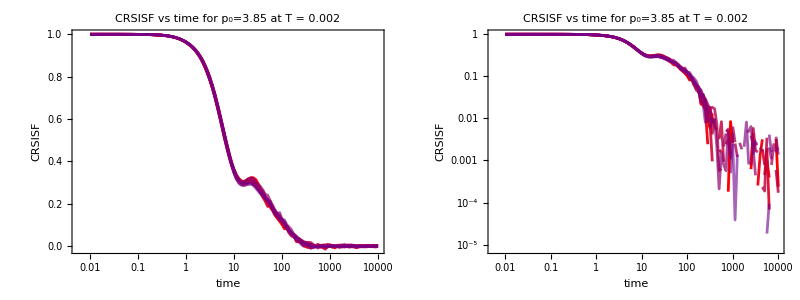

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>40&)][[1,1]],{i,10}]
```

{64,64,64,64,64,64,64,64,64,64}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,100,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.00880758,0.00615077,0.00675317,0.00769708,0.00661075,0.00616361,0.00451894,0.00775556,0.00738106,0.00617613}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(#<noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{80,79,82,81,81,84,82,83,81,79}

```mathematica
initialPlateau[[curP,curT]]=0.6;
initialBeta[[curP,curT]]=0.7;
initialTau[[curP,curT]]=4000.;
betaConstraints[[curP,curT]]=1.0>β>0.3;
plateauConstraints[[curP,curT]]=0.5>G>0.42;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT]],plateauConstraints[[curP,curT]],50000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.49983,0.447909,0.420058,0.456359,0.452407,0.499781,0.468801,0.42209,0.420485,0.420122}

0.4510.031

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{56.4377,70.2617,73.1253,70.5943,67.6436,59.091,68.0783,85.0929,76.8628,75.4234}

70.8.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.767173,0.911613,0.864318,0.861117,0.90829,0.753461,0.81885,0.951027,0.883832,0.938634}

0.870.07

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],10000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],10000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.0025

```mathematica
curP=1;curT=6;
```

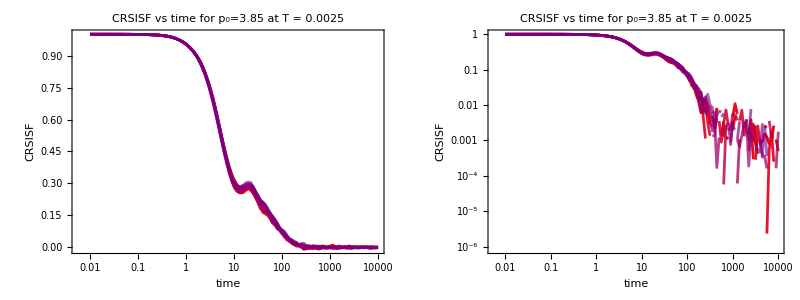

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>40&)][[1,1]],{i,10}]
```

{64,64,64,64,64,64,64,64,64,64}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,90,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.00757576,0.0103482,0.00734468,0.00813785,0.00856768,0.00638611,0.00524985,0.00680461,0.00718339,0.00765731}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(#<noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{76,78,77,79,77,79,81,80,77,82}

```mathematica
initialPlateau[[curP,curT]]=0.6;
initialBeta[[curP,curT]]=0.7;
initialTau[[curP,curT]]=4000.;
betaConstraints[[curP,curT]]=1.0>β>0.3;
plateauConstraints[[curP,curT]]=0.45>G>0.40;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT]],plateauConstraints[[curP,curT]],50000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],
StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.449035,0.400179,0.449381,0.448892,0.400069,0.449899,0.400293,0.449475,0.449931,0.44985}

0.4350.024

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],
StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{49.4781,51.607,53.5683,45.457,58.1537,50.1471,57.2416,46.4648,54.3279,54.9149}

52.4.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],
StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.951767,0.829558,0.917669,0.810922,0.92691,0.934503,0.879786,0.811048,0.999898,0.903788}

0.900.06

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],2000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],2000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.00385

```mathematica
curP=1;curT=5;
```

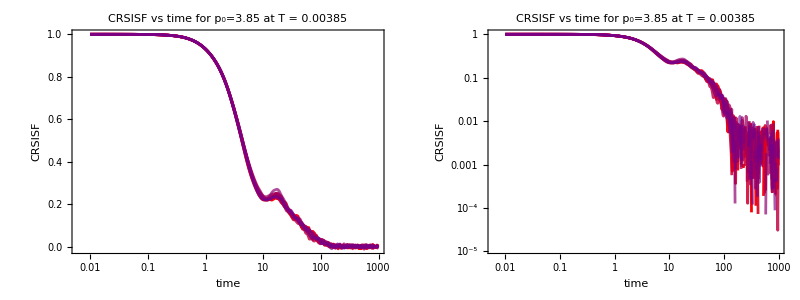

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,310,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.011664,0.0114456,0.0111428,0.012164,0.0113367,0.0114609,0.0131072,0.0106703,0.011841,0.0120477}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>25&)][[1,1]],{i,10}]
```

{221,221,221,221,221,221,221,221,221,221}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(#<noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{287,286,290,286,288,293,290,290,292,285}

```mathematica
initialPlateau[[curP,curT]]=0.6;
initialBeta[[curP,curT]]=0.7;
initialTau[[curP,curT]]=4000.;
betaConstraints[[curP,curT]]=1.0>β>0.3;
plateauConstraints[[curP,curT]]=0.48>G>0.37;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT]],plateauConstraints[[curP,curT]],50000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.479569,0.370021,0.409487,0.470371,0.395828,0.370061,0.370045,0.370307,0.370148,0.39086}

0.400.04

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{25.4657,37.7611,30.5531,28.689,30.8838,36.28,36.241,37.8125,36.8372,34.1982}

33.4.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.755037,0.910287,0.864932,0.95109,0.999633,0.881692,0.901651,0.998747,0.930931,0.999792}

0.920.08

```mathematica
Around[Mean[Table[fittingsTest[[i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittingsTest[[i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

36.63.5

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.736288,0.954341,0.873155,0.950089,0.999629,0.921146,0.945348,0.999005,0.973107,0.999739}

```mathematica
fittingsTest=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT]],plateauConstraints[[curP,curT]],50000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

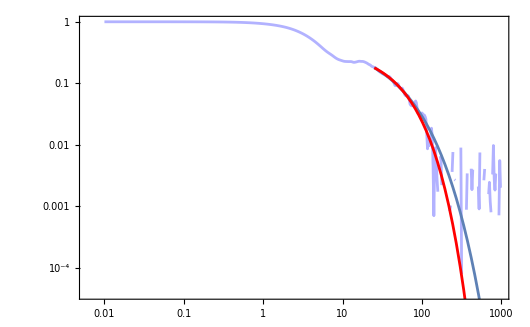

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],5000}],LogLogPlot[fittingsTest[[i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],5000},PlotStyle->Red]],{i,1,1}]
```

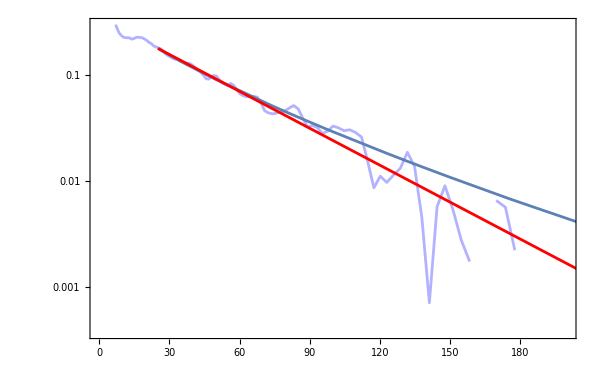

```mathematica
Table[Show[ListLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotRange->{{0,200},{0,0.3}},ImageSize->600,PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],5000}],LogPlot[fittingsTest[[i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],5000},PlotStyle->Red]],{i,1,1}]
```

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],5000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],1000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.005

```mathematica
curP=1;curT=4;
```

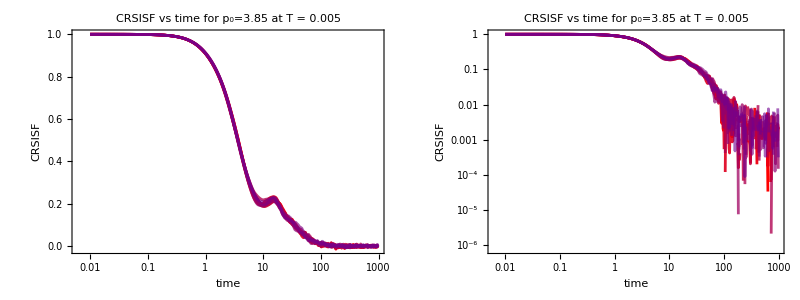

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>20&)][[1,1]],{i,10}]
```

{212,212,212,212,212,212,212,212,212,212}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,300,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.0102266,0.0123582,0.00960793,0.0116115,0.0115849,0.00897379,0.0110524,0.0102787,0.0127028,0.00994276}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(#<noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{277,274,277,277,270,278,277,276,282,288}

```mathematica
initialPlateau[[curP,curT]]=0.6;
initialBeta[[curP,curT]]=0.7;
initialTau[[curP,curT]]=4000.;
betaConstraints[[curP,curT]]=1.0>β>0.3;
plateauConstraints[[curP,curT]]=0.48>G>0.36;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT]],plateauConstraints[[curP,curT]],50000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.479894,0.442185,0.475569,0.374209,0.479799,0.479939,0.360295,0.366583,0.360015,0.424704}

0.420.05

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{20.3693,23.7211,20.0716,27.3103,17.761,19.4686,26.7243,24.6746,29.0158,21.5749}

23.4.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.829434,0.999766,0.896721,0.99558,0.738822,0.79679,0.972196,0.999591,0.945088,0.840715}

0.900.10

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],1000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],1000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.01

```mathematica
curP=1;curT=3;
```

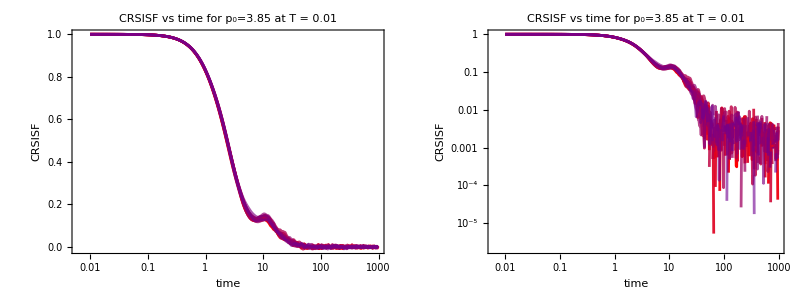

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>15&)][[1,1]],{i,10}]
```

{199,199,199,199,199,199,199,199,199,199}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,250,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.00837897,0.0106634,0.00951054,0.0121956,0.0114726,0.0127704,0.0102215,0.0121172,0.0110944,0.01065}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(#<noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{242,244,232,241,238,247,230,239,235,228}

```mathematica
initialPlateau[[curP,curT]]=0.6;
initialBeta[[curP,curT]]=0.7;
initialTau[[curP,curT]]=4000.;
betaConstraints[[curP,curT]]=1.0>β>0.4;
plateauConstraints[[curP,curT]]=0.5>G>0.4;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT]],plateauConstraints[[curP,curT]],50000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.49845,0.499605,0.499706,0.499574,0.40029,0.409313,0.497076,0.499622,0.4291,0.499869}

0.470.04

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{7.53372,7.92773,7.98507,8.63708,9.54208,10.9703,8.88343,8.20377,10.1648,8.84876}

8.91.1

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.859761,0.688056,0.657493,0.715225,0.776579,0.769904,0.717903,0.77217,0.667218,0.815187}

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],10000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,fitEndPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.016

```mathematica
curP=1;curT=2;
```

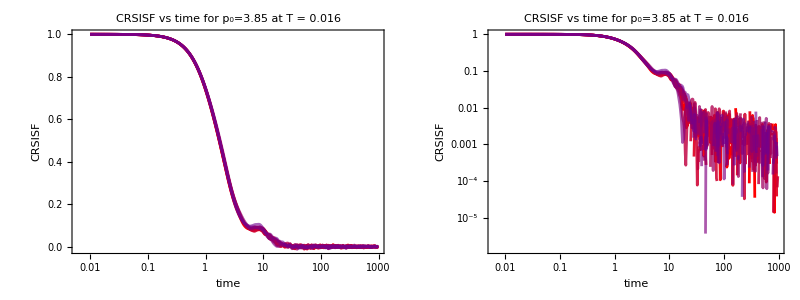

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>9&)][[1,1]],{i,10}]
```

{177,177,177,177,177,177,177,177,177,177}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,250,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.00915088,0.00880857,0.00977755,0.00912401,0.00966155,0.00971626,0.00798533,0.00932131,0.00891167,0.00824655}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(#<noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{205,214,216,213,203,215,217,220,201,219}

```mathematica
initialPlateau[[curP,curT]]=0.6;
initialBeta[[curP,curT]]=0.7;
initialTau[[curP,curT]]=4000.;
betaConstraints[[curP,curT]]=1.0>β>0.4;
plateauConstraints[[curP,curT]]=0.48>G>0.35;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT]],plateauConstraints[[curP,curT]],50000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.350441,0.479284,0.370944,0.479296,0.479951,0.473326,0.479341,0.351406,0.479877,0.478451}

0.440.06

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{6.02715,5.22126,6.60654,5.37571,5.39535,5.67817,5.20164,6.39254,5.06295,5.02815}

5.60.6

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.938817,0.896251,0.999671,0.959631,0.999958,0.997059,0.951292,0.94692,0.999907,0.792616}

0.950.06

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],1000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,fitEndPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.0039

```mathematica
curP=1;curT=1;
```

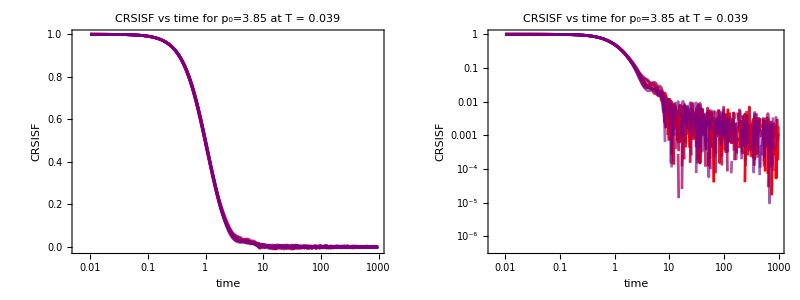

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>1&)][[1,1]],{i,10}]
```

{82,82,82,82,82,82,82,82,82,82}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(#<8*10^-2&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{122,122,121,124,120,124,122,121,119,122}

```mathematica
initialPlateau[[curP,curT]]=0.6;
initialBeta[[curP,curT]]=0.7;
initialTau[[curP,curT]]=4000.;
betaConstraints[[curP,curT]]=1.0>β>0.3;
plateauConstraints[[curP,curT]]=1.0>G>0.4;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT]],plateauConstraints[[curP,curT]],50000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999999}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
```

{1.1524,1.15422,1.17183,1.1944,1.18236,1.19155,1.17503,1.17431,1.16033,1.16691}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.999999,0.999999,0.999999,0.999999,0.999999,0.999999,0.999996,0.999999,0.999999,0.999999}

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],1000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],100}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### summary

#### fitting results

```mathematica
fittings[[curP]]
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
fittings[[1]]={{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}};
```

```mathematica
Table[Dimensions[fittings[[curP,T]]],{T,Length[fittings[[curP]]]}]
```

{{10},{10},{0},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10}}

#### fitting parameters

```mathematica
tauAlphaResults[[curP]]=Table[Around[Mean[Table[fittings[[curP,T,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,T]]]}]],StandardDeviation[Table[fittings[[curP,T,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,T]]]}]]],{T,Length[temperatures[[curP]]]}];
plateauResults[[curP]]=Table[Around[Mean[Table[fittings[[curP,T,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,T]]]}]],StandardDeviation[Table[fittings[[curP,T,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,T]]]}]]],{T,Length[temperatures[[curP]]]}];
betaResults[[curP]]=Join[Table[Around[Mean[Table[fittings[[curP,T,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,T]]]}]],StandardDeviation[Table[fittings[[curP,T,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,T]]]}]]],{T,Length[temperatures[[curP]]]}]];
```

```mathematica
numExp[[curP]]=Table[Count[Table[fittings[[curP,T,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,T]]]}],_?(#>0.95&)],{T,Length[temperatures[[curP]]]}]
```

{10,6,3,4,4,2,1,4,0,0,0,0,0,0,0,0,0}

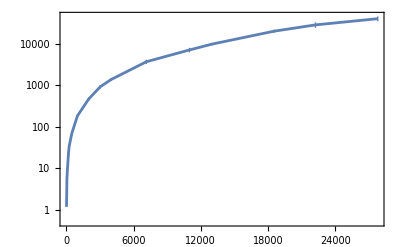

```mathematica
ListLogPlot[Table[{1/temperatures[[curP,T]],tauAlphaResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],PlotRange->{All,All},Joined->True]
```

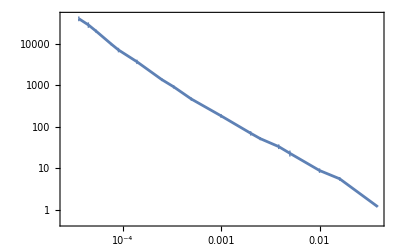

```mathematica
ListLogLogPlot[Table[{temperatures[[curP,T]],tauAlphaResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],Joined->True]
```

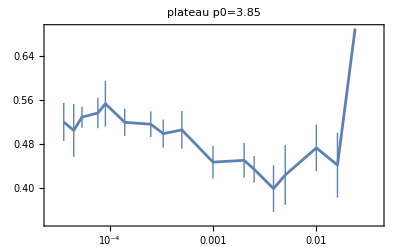

```mathematica
ListLogLinearPlot[Table[{temperatures[[curP,T]],plateauResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],Joined->True,PlotLabel->"plateau p0="<>ToString[p0s[[curP]]]]
```

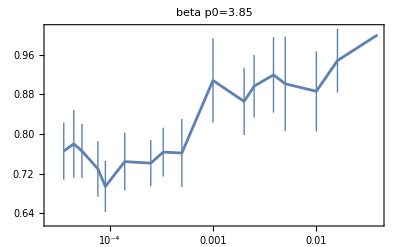

```mathematica
ListLogLinearPlot[Table[{temperatures[[curP,T]],betaResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],Joined->True,PlotLabel->"beta p0="<>ToString[p0s[[curP]]]]
```

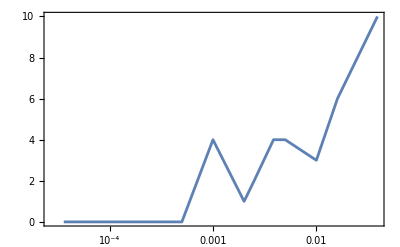

```mathematica
ListLogLinearPlot[Table[{temperatures[[curP,T]],numExp[[curP,T]]},{T,Length[temperatures[[curP]]]}],Joined->True]
```

## p_(0=)3.825

### T=0.0005

```mathematica
curP=2;curT=16;
```

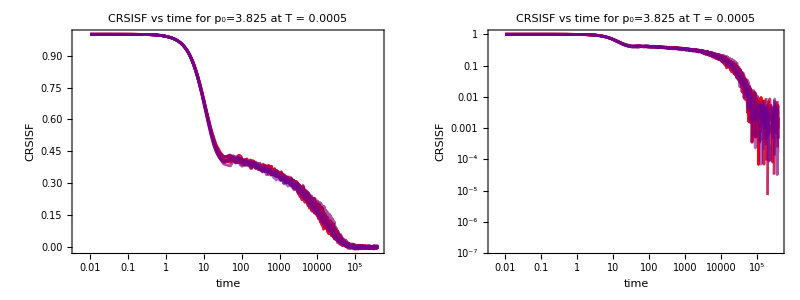

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
noiseLevel[[curP,curT]]=Table[4*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,580,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.0130374,0.0131788,0.0138906,0.0131955,0.0111685,0.0174491,0.0133006,0.0129276,0.0123563,0.0116806}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>150&)][[1,1]],{i,10}]
```

{299,299,299,299,299,299,299,299,299,299}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{564,550,545,554,560,557,551,564,557,545}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{641,641,641,641,641,641,639,640,640,641}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=10000.;
betaConstraints[[curP,curT]]={1.0>β>0.3,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.3,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.403385,0.399401,0.415046,0.395366,0.396059,0.403607,0.411805,0.386228,0.399066,0.405327}

0.4020.008

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{15300.5,10788.3,9323.98,13261.9,12968.2,15128.8,11629.6,18720.8,13189.,10151.5}

1.300.2810^4

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.696892,0.785799,0.712294,0.793975,0.722199,0.685586,0.67621,0.727496,0.723892,0.688026}

0.720.04

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
""
```

### T=0.0067

```mathematica
curP=2;curT=15;
```

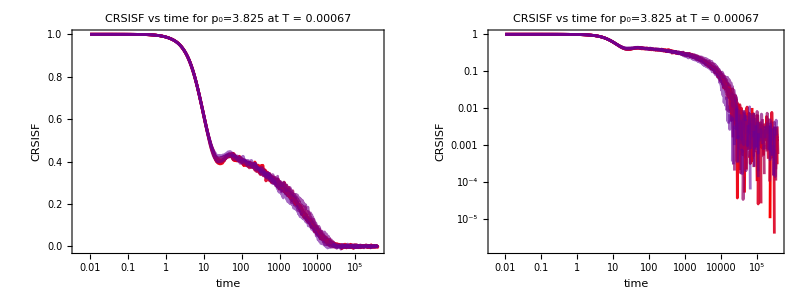

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
noiseLevel[[curP,curT]]=Table[4*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,540,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.0108536,0.0115378,0.0117797,0.0127114,0.0108717,0.011436,0.0113481,0.0118417,0.0124423,0.0116954}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>150&)][[1,1]],{i,10}]
```

{299,299,299,299,299,299,299,299,299,299}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{511,518,506,524,510,513,499,513,524,497}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{641,641,641,641,641,641,639,640,640,641}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=4000.;
betaConstraints[[curP,curT]]={1.0>β>0.3,0.99>β>0.72,0.99>β>0.72,0.99>β>0.72,0.99>β>0.72,0.99>β>0.73,0.99>β>0.73,0.99>β>0.72,0.99>β>0.72,0.99>β>0.74};
plateauConstraints[[curP,curT]]={0.43>G>0.30,0.42>G>0.4,0.42>G>0.4,0.42>G>0.4,0.42>G>0.4,0.42>G>0.4,0.42>G>0.4,0.42>G>0.4,0.42>G>0.4,0.5>G>0.4};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],5500>τ>3500}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.426379,0.429999,0.410412,0.416764,0.406357,0.41144,0.429518,0.422123,0.42831,0.422477}

0.4200.009

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{4041.8,4077.29,4459.95,4759.57,4576.19,5499.9,3799.15,4389.69,5499.99,3500.01}

4460.663.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.688712,0.686759,0.713086,0.703509,0.725564,0.719887,0.69398,0.682589,0.641573,0.706355}

0.6960.024

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.001

```mathematica
curP=2;curT=14;
```

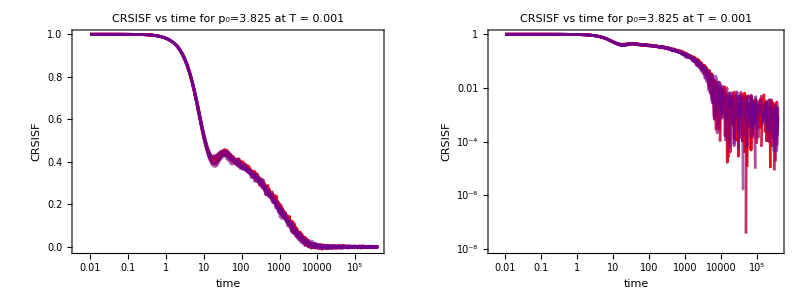

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
noiseLevel[[curP,curT]]=Table[4*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,500,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.0097235,0.00938996,0.00991431,0.00839431,0.00894269,0.0101027,0.00937441,0.00934384,0.00892394,0.00983112}

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>200&)][[1,1]],{i,10}]
```

{312,312,312,312,312,312,312,312,312,312}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{469,454,449,452,460,456,466,455,446,477}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{641,641,641,641,641,639,637,640,641,641}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=2000.;
betaConstraints[[curP,curT]]={1.0>β>0.3,0.75>β>0.73,0.73>β>0.71,0.73>β>0.71,0.75>β>0.73,0.75>β>0.73,0.75>β>0.73,0.75>β>0.73,0.75>β>0.73,0.75>β>0.70};
plateauConstraints[[curP,curT]]=0.5>G>0.3;
tauConstraints[[curP,curT]]=0.45>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,i]],plateauConstraints[[curP,curT]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.451863,0.443004,0.463121,0.445641,0.451235,0.438285,0.435197,0.457696,0.45455,0.450016}

0.4490.009

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{1270.57,1265.52,1123.16,1185.55,1089.03,1288.13,1218.55,1056.59,996.165,1165.01}

1166.99.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.675628,0.73001,0.729904,0.729995,0.73001,0.738348,0.73001,0.749976,0.730103,0.700004}

0.7240.021

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.0015

```mathematica
curP=2;curT=13;
```

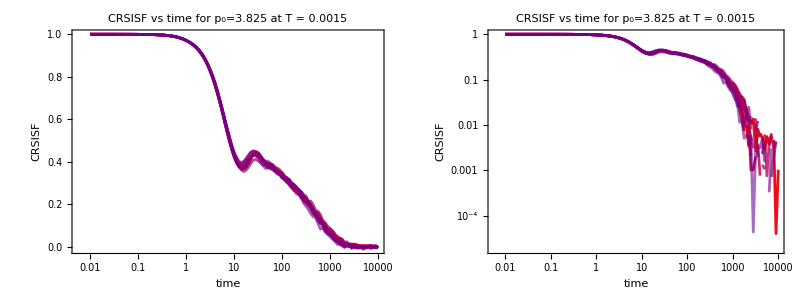

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>100&)][[1,1]],{i,10}]
```

{71,71,71,71,71,71,71,71,71,71}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,10,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{1.12869,1.12666,1.12876,1.12685,1.12426,1.12885,1.11858,1.1269,1.13853,1.13581}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <10^-2&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{95,100,95,98,100,97,99,95,96,95}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,111,111,111,111,111,111}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=500.;
betaConstraints[[curP,curT]]={1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5};
plateauConstraints[[curP,curT]]=0.46>G>0.42;
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT]],10000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.428782,0.453977,0.42001,0.450385,0.454885,0.445572,0.420025,0.420012,0.459967,0.420012}

0.4370.017

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{492.932,450.055,509.825,455.909,455.794,454.194,582.238,521.996,375.797,479.116}

478.55.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.923268,0.772431,0.899636,0.714767,0.798895,0.906032,0.838907,0.900845,0.839573,0.996892}

0.860.08

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.002

```mathematica
curP=2;curT=12;
```

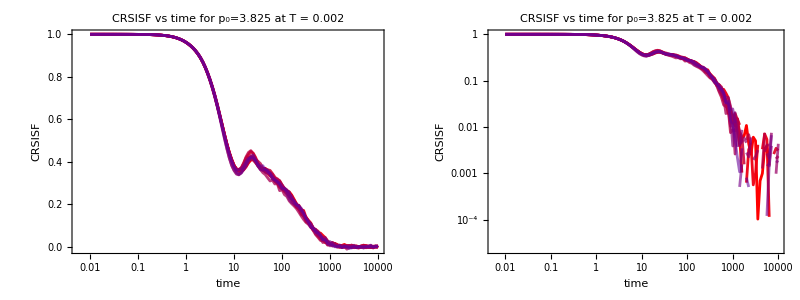

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>50&)][[1,1]],{i,10}]
```

{65,65,65,65,65,65,65,65,65,65}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,100,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.00911031,0.011709,0.00837997,0.00813552,0.0110902,0.0123001,0.00944758,0.00905809,0.0108352,0.00839542}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{93,92,94,93,89,89,92,90,92,91}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,111,111,111,111,111,111}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=500.;
betaConstraints[[curP,curT]]={1.0>β>0.5,0.95>β>0.92,0.95>β>0.89,0.95>β>0.93,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89};
plateauConstraints[[curP,curT]]=0.6>G>0.3;
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT]],10000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.416623,0.439739,0.447021,0.540919,0.437689,0.425013,0.433759,0.433754,0.475688,0.427832}

0.450.04

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{282.376,270.164,240.025,191.477,251.524,232.816,269.368,263.207,227.645,271.274}

250.27.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.967318,0.837858,0.850103,0.708391,0.983659,0.856882,0.88852,0.884942,0.759726,0.931294}

0.870.09

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.0025

```mathematica
curP=2;curT=11;
```

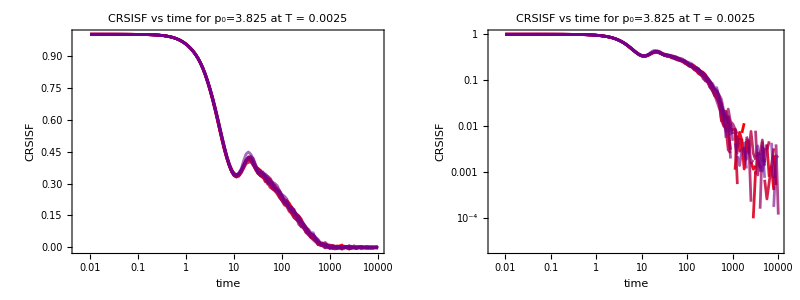

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>50&)][[1,1]],{i,10}]
```

{65,65,65,65,65,65,65,65,65,65}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,95,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.0129647,0.00824241,0.00887578,0.00825068,0.0109408,0.0102842,0.0103718,0.00790421,0.0092797,0.00972031}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{86,92,88,88,90,88,91,87,87,89}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,111,111,111,111,111,111}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.9;
initialTau[[curP,curT]]=230.;
betaConstraints[[curP,curT]]={1.0>β>0.5,0.95>β>0.92,0.95>β>0.89,0.95>β>0.93,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89};
plateauConstraints[[curP,curT]]=0.6>G>0.2;
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.454254,0.407274,0.456211,0.452712,0.472429,0.389392,0.525869,0.402393,0.518011,0.447633}

0.450.05

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{179.18,202.686,161.483,152.401,144.405,208.2,137.989,183.955,151.357,181.033}

170.24.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.838909,0.922191,0.837403,0.822474,0.751764,0.949821,0.705588,0.999382,0.771411,0.817555}

0.840.09

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.0031

```mathematica
curP=2;curT=10;
```

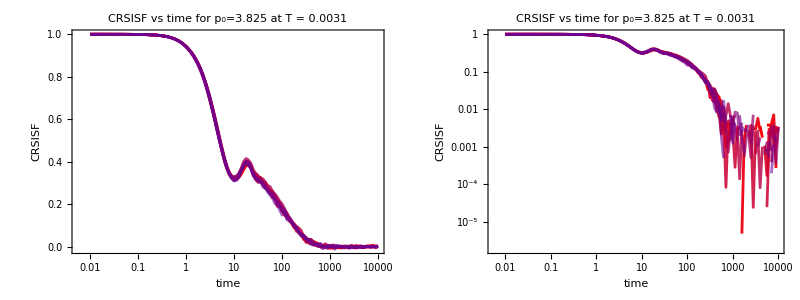

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>40&)][[1,1]],{i,10}]
```

{64,64,64,64,64,64,64,64,64,64}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,90,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.0107172,0.00998618,0.00950619,0.00731936,0.0070063,0.00663028,0.00865917,0.0124246,0.00812704,0.012863}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{86,84,84,84,86,86,85,83,85,85}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,111,111,111,111,111,111}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.9;
initialTau[[curP,curT]]=230.;
betaConstraints[[curP,curT]]={1.0>β>0.5,0.95>β>0.92,0.95>β>0.89,0.95>β>0.93,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89};
plateauConstraints[[curP,curT]]=0.45>G>0.4;
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT]],10000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.449935,0.449973,0.449958,0.415124,0.426481,0.449916,0.402143,0.449859,0.40006,0.449965}

0.4340.021

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{109.99,114.503,107.809,124.949,125.164,121.242,128.092,108.287,128.3,101.275}

117.10.

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.00385

```mathematica
curP=2;curT=9;
```

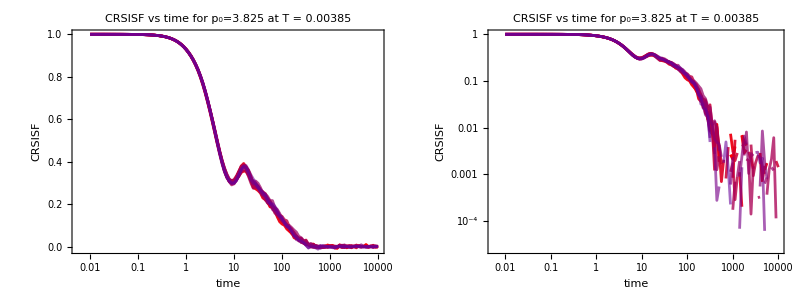

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>40&)][[1,1]],{i,10}]
```

{64,64,64,64,64,64,64,64,64,64}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,90,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.0133544,0.0104595,0.00849258,0.0103281,0.00712834,0.00695378,0.00721586,0.00990416,0.00826472,0.00614976}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{80,82,82,81,82,83,84,82,80,80}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,111,111,111,111,111,111}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.95;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.5,0.95>β>0.92,0.95>β>0.89,0.95>β>0.93,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89};
plateauConstraints[[curP,curT]]=0.42>G>0.3;
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT]],10000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.419866,0.419875,0.392765,0.419936,0.37485,0.401339,0.419947,0.41992,0.376878,0.394362}

0.4040.018

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{80.7383,73.8862,85.4155,80.9037,100.993,82.0944,91.403,81.0739,92.6287,90.7583}

86.8.

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.005

```mathematica
curP=2;curT=8;
```

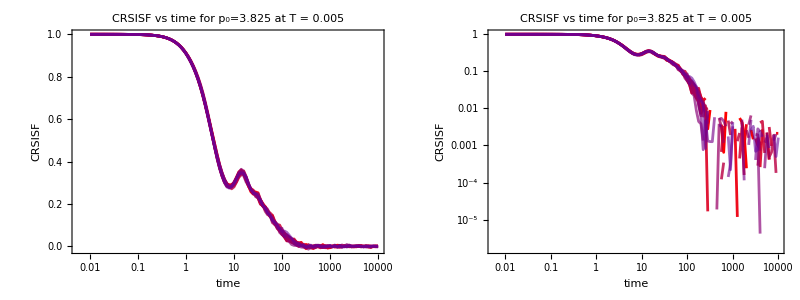

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>30&)][[1,1]],{i,10}]
```

{61,61,61,61,61,61,61,61,61,61}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,85,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.00937854,0.00742769,0.00756802,0.00633173,0.00527505,0.00882133,0.0089791,0.00930331,0.00854337,0.0082437}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{76,79,76,80,80,76,78,74,76,78}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,111,111,111,111,111,111}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.95;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.5,0.95>β>0.92,0.95>β>0.89,0.95>β>0.93,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89};
plateauConstraints[[curP,curT]]=0.42>G>0.3;
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT]],10000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.412968,0.419972,0.406748,0.419849,0.394514,0.419955,0.419931,0.41997,0.419907,0.419968}

0.4150.009

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{53.1653,55.3309,54.0013,56.6053,55.589,51.6224,51.6573,52.5935,53.0904,54.6109}

53.81.7

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.0063

```mathematica
curP=2;curT=7;
```

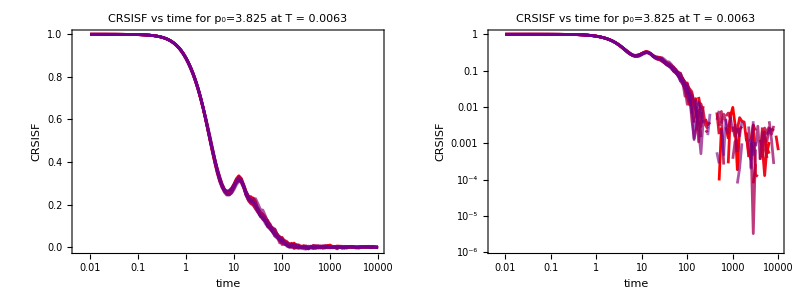

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>30&)][[1,1]],{i,10}]
```

{61,61,61,61,61,61,61,61,61,61}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,78,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.00830687,0.00880413,0.00940623,0.0107708,0.00948092,0.0100101,0.00862062,0.00952887,0.0085895,0.0100251}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{75,73,74,74,75,72,73,74,72,72}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,111,111,111,111,111,111}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.95;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.5,0.95>β>0.92,0.95>β>0.89,0.95>β>0.93,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89};
plateauConstraints[[curP,curT]]=0.41>G>0.37;
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT]],10000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.395255,0.39427,0.386124,0.370253,0.37507,0.401994,0.409967,0.409951,0.398325,0.399091}

0.3940.013

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{39.051,37.0528,42.5083,42.2121,38.73,35.6131,38.8573,42.5882,36.7962,35.9171}

38.92.7

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],1000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.008

```mathematica
curP=2;curT=6;
```

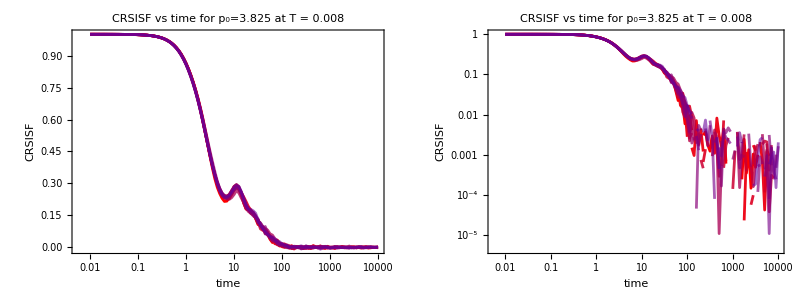

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>25&)][[1,1]],{i,10}]
```

{59,59,59,59,59,59,59,59,59,59}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,78,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.00613176,0.00731186,0.00780141,0.00698466,0.00676751,0.0073471,0.00794354,0.00671601,0.00795257,0.00928246}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{69,70,73,71,71,71,72,71,73,73}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,111,111,111,111,111,111}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.95;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.5,0.95>β>0.92,0.95>β>0.89,0.95>β>0.93,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89};
plateauConstraints[[curP,curT]]=0.42>G>0.3;
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT]],10000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.416585,0.412159,0.41979,0.419556,0.413826,0.354963,0.41971,0.352683,0.419201,0.41991}

0.4050.027

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{25.1554,26.5198,24.8628,25.3739,25.0729,31.5526,25.9947,30.185,25.5648,26.7751}

26.72.3

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],1000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.01

```mathematica
curP=2;curT=5;
```

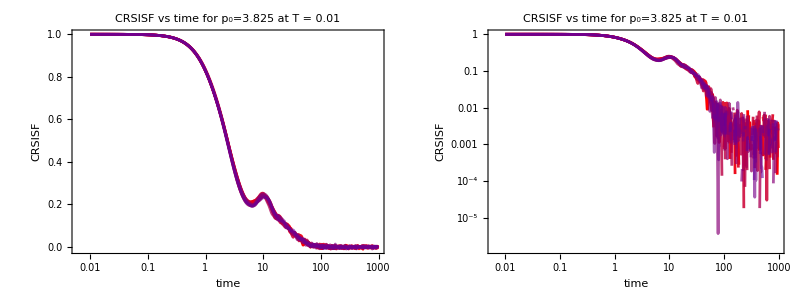

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>20&)][[1,1]],{i,10}]
```

{212,212,212,212,212,212,212,212,212,212}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,280,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.0107102,0.00848255,0.0141199,0.0104227,0.0105946,0.0102974,0.0107389,0.00994512,0.0109981,0.00977003}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{249,264,260,257,263,262,266,254,257,261}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{380,380,380,380,380,380,380,380,380,380}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.95;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.5,0.95>β>0.92,0.95>β>0.89,0.95>β>0.93,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89};
plateauConstraints[[curP,curT]]=0.42>G>0.32;
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT]],10000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.41893,0.321248,0.419826,0.389644,0.404927,0.320235,0.419843,0.389671,0.412188,0.324265}

0.380.04

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{17.9652,20.9706,17.3871,16.8658,17.4781,20.3056,16.5587,18.7798,18.4813,21.4506}

18.61.7

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],1000}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.016

```mathematica
curP=2;curT=4;
```

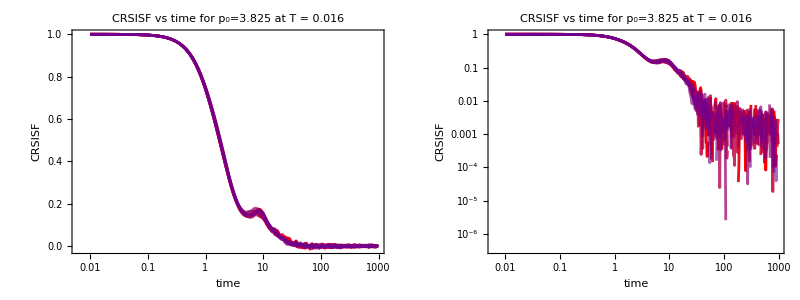

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>10&)][[1,1]],{i,10}]
```

{182,182,182,182,182,182,182,182,182,182}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,240,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.0102606,0.0110751,0.0123232,0.0102986,0.0112356,0.0100973,0.0114052,0.0126441,0.0123383,0.00970193}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{239,232,224,227,230,229,226,220,227,225}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,111,111,111,111,111,111}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.95;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.5,0.95>β>0.92,0.95>β>0.89,0.95>β>0.93,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89};
plateauConstraints[[curP,curT]]=0.45>G>0.35;
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT]],10000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.449861,0.449933,0.449912,0.409679,0.44899,0.44984,0.426847,0.449977,0.449929,0.449953}

0.4430.014

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{7.22142,7.86412,8.35744,8.83946,8.2567,7.29953,8.67808,8.14497,8.46033,8.62966}

8.20.6

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.75845,0.879973,0.919144,0.999296,0.975958,0.876986,0.943982,0.99997,0.999808,0.999932}

0.90.6

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],500}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.03105

```mathematica
curP=2;curT=3;
```

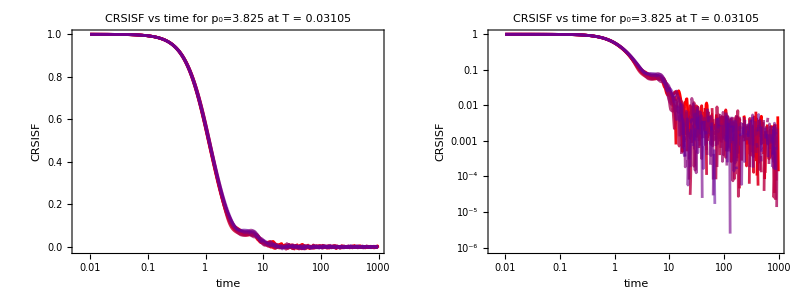

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>8&)][[1,1]],{i,10}]
```

{172,172,172,172,172,172,172,172,172,172}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,220,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.0104124,0.00954417,0.00862504,0.00906437,0.0101294,0.00836077,0.00977642,0.00835588,0.00813711,0.00774749}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{202,189,202,191,186,182,195,195,190,203}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,111,111,111,111,111,111}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.95;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.7,0.95>β>0.92,0.95>β>0.89,0.95>β>0.93,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89};
plateauConstraints[[curP,curT]]=0.5>G>0.42;
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT]],10000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.420088,0.425844,0.426639,0.499823,0.499785,0.499353,0.496774,0.499259,0.499474,0.420136}

0.470.04

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.70004,0.8974,0.700943,0.999876,0.999845,0.999668,0.836913,0.999504,0.999628,0.700079}

0.90.5

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{2.31033,3.00386,2.39348,3.38551,3.32798,3.22229,2.46589,3.52741,3.51878,2.42698}

3.00.5

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],50}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.039

```mathematica
curP=2;curT=2;
```

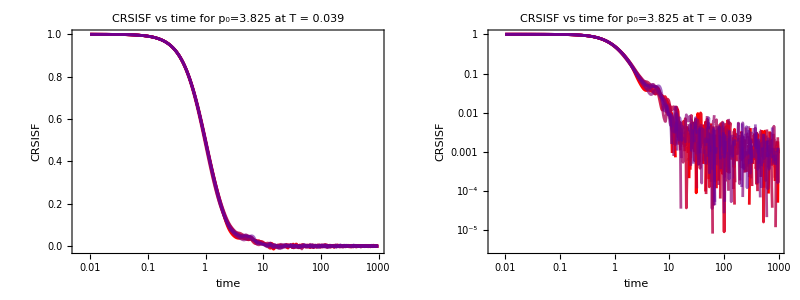

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>7&)][[1,1]],{i,10}]
```

{166,166,166,166,166,166,166,166,166,166}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,200,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.00865008,0.00836514,0.00800923,0.00715021,0.00803607,0.00860872,0.00868399,0.00871876,0.00983146,0.00813568}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{185,184,184,183,195,170,181,180,179,182}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,111,111,111,111,111,111}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.95;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.7,0.95>β>0.92,0.95>β>0.89,0.95>β>0.93,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89};
plateauConstraints[[curP,curT]]=0.4>G>0.32;
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT]],10000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.353593,0.363902,0.327691,0.320212,0.320245,0.39609,0.339668,0.359923,0.355435,0.39919}

0.3540.028

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{2.3498,2.44038,2.30105,1.76619,1.93793,2.2706,2.69929,2.65397,1.88161,2.59493}

2.290.33

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.823621,0.884333,0.781673,0.700158,0.700167,0.997041,0.950233,0.984077,0.757374,0.999291}

0.860.33

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],50}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.063

```mathematica
curP=2;curT=1;
```

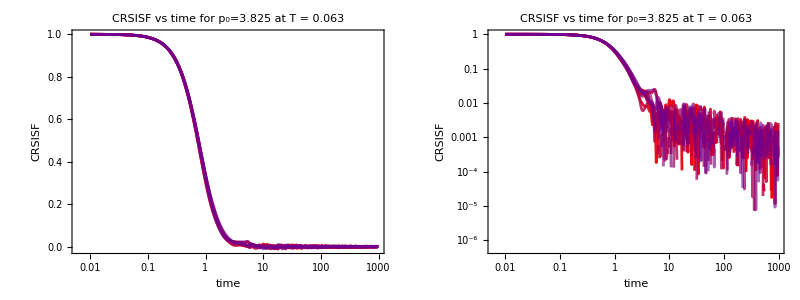

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>1&)][[1,1]],{i,10}]
```

{82,82,82,82,82,82,82,82,82,82}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <3*10^-2&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{123,120,118,120,118,123,120,125,123,122}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{380,380,380,380,380,380,380,380,380,380}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.95;
initialTau[[curP,curT]]=100.;
betaConstraints[[curP,curT]]={1.0>β>0.5,0.95>β>0.92,0.95>β>0.89,0.95>β>0.93,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89,0.95>β>0.89};
plateauConstraints[[curP,curT]]=1.0>G>0.3;
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT]],10000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.999996,0.999996,0.999996,0.999994,0.999995,0.999996,0.999996,0.999996,0.999996,0.999996}

0.99999579

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.793032,0.790489,0.775013,0.757066,0.751017,0.814992,0.791936,0.825984,0.832323,0.768475}

0.7900.028

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,1,10}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### Summary

#### fitting results

```mathematica
Table[Dimensions[fittings[[curP,T]]],{T,Length[temperatures[[curP]]]}]
```

{{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10}}

```mathematica
fittings[[curP]]
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
fittings[[2]]={{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}};
```

#### loose constraints

```mathematica
tauAlphaResults[[curP]]=Table[Around[Mean[Table[fittings[[curP,T,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,T]]]}]],StandardDeviation[Table[fittings[[curP,T,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,T]]]}]]],{T,Length[temperatures[[curP]]]}];
plateauResults[[curP]]=Table[Around[Mean[Table[fittings[[curP,T,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,T]]]}]],StandardDeviation[Table[fittings[[curP,T,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,T]]]}]]],{T,Length[temperatures[[curP]]]}];
betaResults[[curP]]=Join[Table[Around[Mean[Table[fittings[[curP,T,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,T]]]}]],StandardDeviation[Table[fittings[[curP,T,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,T]]]}]]],{T,Length[temperatures[[curP]]]}]];
```

```mathematica
numExp[[curP]]=Table[Count[Table[fittings[[curP,T,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,T]]]}],_?(#>0.99&)],{T,Length[temperatures[[curP]]]}]
```

{10,10,10,1,5,5,7,4,3,2,1,0,1,0,0,0}

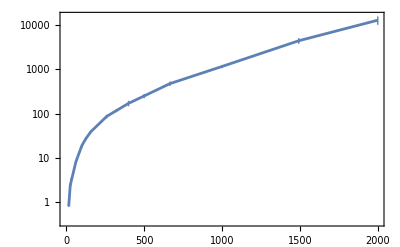

```mathematica
ListLogPlot[Table[{1/temperatures[[curP,T]],tauAlphaResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],Joined->True]
```

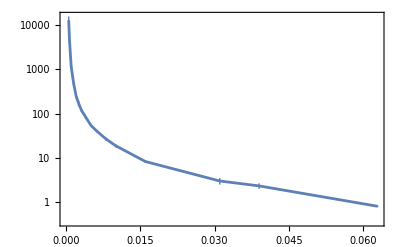

```mathematica
ListLogPlot[Table[{temperatures[[curP,T]],tauAlphaResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],Joined->True]
```

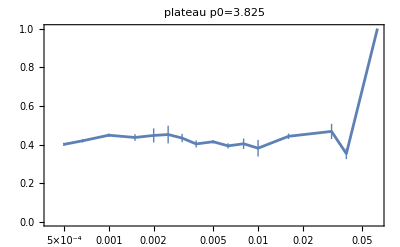

```mathematica
ListLogLinearPlot[Table[{temperatures[[curP,T]],plateauResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],PlotRange->All,Joined->True,PlotLabel->"plateau p0="<>ToString[p0s[[curP]]]]
```

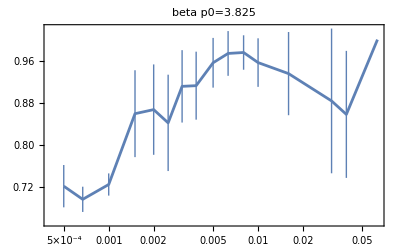

```mathematica
ListLogLinearPlot[Table[{temperatures[[curP,T]],betaResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],Joined->True,PlotLabel->"beta p0="<>ToString[p0s[[curP]]]]
```

#### force exponential

```mathematica
tauAlphaResults[[curP]]=Table[Around[Mean[Table[fittings[[curP,T,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,T]]]}]],StandardDeviation[Table[fittings[[curP,T,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,T]]]}]]],{T,Length[temperatures[[curP]]]}]
```

{1.040.14,1.760.15,3.60.4,9.11.1,19.51.0,27.01.6,39.62.6,57.4.,96.7.,129.5.,203.13.,282.16.,549.68.,1185.105.,4531.632.,1.310.2710^4}

```mathematica
plateauResults[[curP]]=Table[Around[Mean[Table[fittings[[curP,T,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,T]]]}]],StandardDeviation[Table[fittings[[curP,T,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,T]]]}]]],{T,Length[temperatures[[curP]]]}]
```

{0.410.09,0.4350.024,0.440.10,0.410.07,0.3660.031,0.4030.017,0.3900.016,0.3980.014,0.3680.018,0.4010.019,0.3930.014,0.4060.012,0.3940.018,0.4440.008,0.4140.005,0.4010.006}

```mathematica
betaResults[[curP]]=Join[Table[Around[1,0],{T,Length[temperatures[[curP]]]-3}],Table[Around[Mean[Table[fittings[[curP,T,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,T]]]}]],StandardDeviation[Table[fittings[[curP,T,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,T]]]}]]],{T,Length[temperatures[[curP]]]-2,Length[temperatures[[curP]]]}]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,0.7330.015,0.7240.007,0.7260.009}

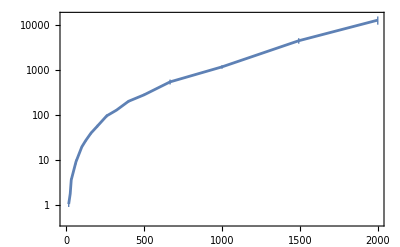

```mathematica
ListLogPlot[Table[{1/temperatures[[curP,T]],tauAlphaResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],Joined->True]
```

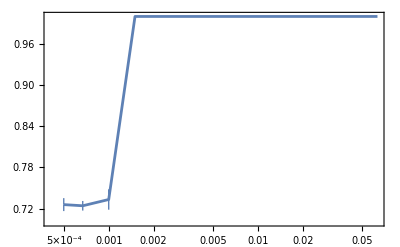

```mathematica
ListLogLinearPlot[Table[{temperatures[[curP,T]],betaResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],Joined->True]
```

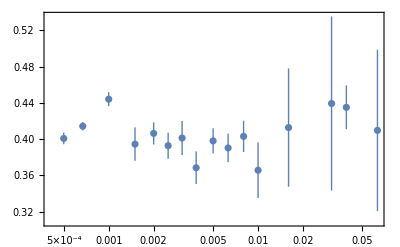

```mathematica
ListLogLinearPlot[Table[{temperatures[[curP,T]],plateauResults[[curP,T]]},{T,Length[temperatures[[curP]]]}]]
```

## p_0=3.80

### T=0.0022

```mathematica
curP=3;curT=14;
```

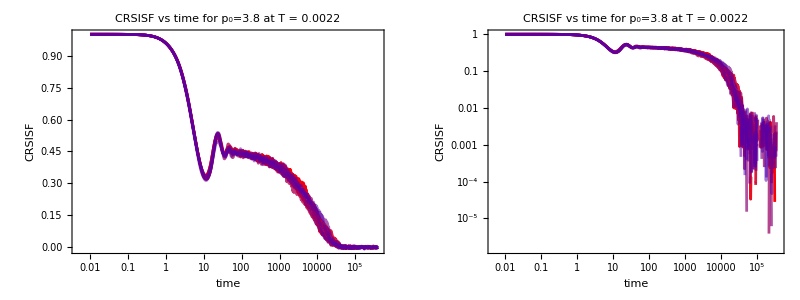

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>200&)][[1,1]],{i,10}]
```

{312,312,312,312,312,312,312,312,312,312}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,550,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.00769683,0.00900992,0.00904933,0.00906933,0.00915631,0.00764469,0.00702427,0.00895774,0.00887142,0.00848803}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{532,527,542,534,534,539,532,537,528,533}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{641,580,580,580,641,640,641,641,640,641}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=10000.;
betaConstraints[[curP,curT]]={1.0>β>0.3,1.0>β>0.999,1.0>β>0.5,1.0>β>0.999,1.0>β>0.5,1.0>β>0.999,1.0>β>0.999,1.0>β>0.5,1.0>β>0.999,1.0>β>0.5};
plateauConstraints[[curP,curT]]={0.9>G>0.3,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.43837,0.436355,0.472111,0.43284,0.467301,0.425387,0.434137,0.455521,0.438459,0.435041}

0.4440.016

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{9440.23,8455.99,7496.64,6940.83,6495.22,9857.81,7310.42,9443.85,8139.25,9485.59}

8.31.210^3

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.983636,0.999999,0.641582,0.91643,0.702348,0.854093,0.999928,0.751113,0.999992,0.79027}

0.860.14

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.0025

```mathematica
curP=3;curT=13;
```

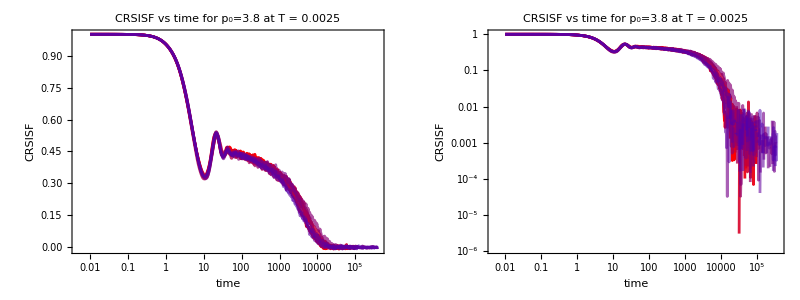

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>100&)][[1,1]],{i,10}]
```

{281,281,281,281,281,282,282,281,281,281}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,530,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.00858923,0.0078489,0.00969463,0.00898112,0.0081291,0.00876074,0.00969097,0.00712261,0.00841604,0.00856404}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{488,511,509,504,500,499,517,490,490,508}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{641,641,641,641,641,641,639,640,640,641}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=10000.;
betaConstraints[[curP,curT]]={1.0>β>0.3,1.0>β>0.9999,1.0>β>0.9999,1.0>β>0.5,1.0>β>0.9999,1.0>β>0.9999,1.0>β>0.5,1.0>β>0.9999,1.0>β>0.9999,1.0>β>0.5};
plateauConstraints[[curP,curT]]={0.44>G>0.3,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.44,0.437264,0.423507,0.439989,0.423553,0.421688,0.438514,0.439762,0.437274,0.439999}

0.4340.008

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{3864.04,4766.53,5090.13,4583.4,5073.75,4963.5,6036.,4280.38,3479.28,3775.04}

4591.765.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.999999,0.932301,0.999995,0.783684,0.939126,0.942472,0.823128,0.999999,0.925909,0.85073}

0.920.08

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.0028

```mathematica
curP=3;curT=12;
```

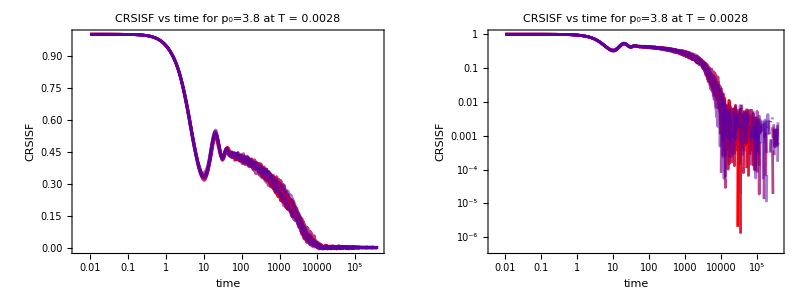

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>200&)][[1,1]],{i,10}]
```

{312,312,312,312,312,312,312,312,312,312}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,500,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.00919784,0.00863507,0.00880113,0.00784102,0.00885903,0.00724949,0.00738514,0.00659384,0.00688603,0.00711779}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{478,479,476,475,490,488,467,477,466,488}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{580,580,580,580,589,640,641,641,640,640}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=3000.;
betaConstraints[[curP,curT]]={1.0>β>0.5,1.0>β>0.9999,1.0>β>0.9999,1.0>β>0.9999,1.0>β>0.9999,1.0>β>0.5,1.0>β>0.9999,1.0>β>0.5,1.0>β>0.5,1.0>β>0.9999};
plateauConstraints[[curP,curT]]={0.9>G>0.3,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.466112,0.417073,0.415921,0.408757,0.432245,0.419347,0.388702,0.42248,0.463607,0.411141}

0.4250.024

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{1840.31,2931.34,2883.58,2345.57,3190.,2758.57,2292.85,2331.02,1916.35,3227.45}

2572.497.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.72291,0.999022,0.980325,0.999853,0.902563,0.879441,0.999836,0.847829,0.845278,0.999996}

0.920.09

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
""
```

### T=0.0031

```mathematica
curP=3;curT=11;
```

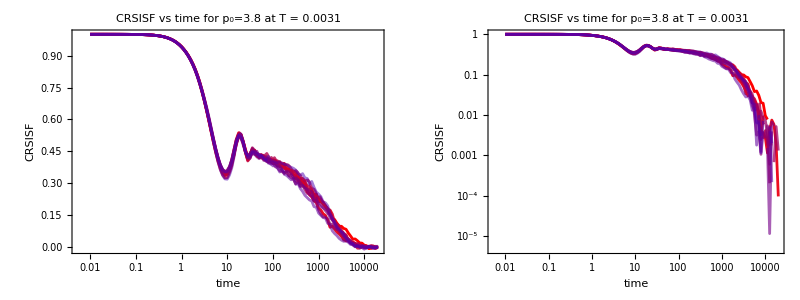

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>70&)][[1,1]],{i,10}]
```

{68,68,68,68,97,68,68,68,68,68}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,110,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.0266634,0.00734891,0.0159784,0.00595264,0.419675,0.0104343,0.010924,0.016188,0.0105678,0.012911}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <10^-2&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{110,108,107,107,157,107,106,106,106,106}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{117,117,113,114,170,117,117,117,117,117}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=10000.;
betaConstraints[[curP,curT]]={1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.9999,1.0>β>0.9999,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.9999};
plateauConstraints[[curP,curT]]={0.9>G>0.3,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.49767,0.460841,0.446366,0.424335,0.448652,0.480709,0.451143,0.437235,0.462731,0.431556}

0.4540.022

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{1390.21,1179.52,1658.19,1656.9,1649.64,1085.5,1362.38,1468.26,967.857,1812.66}

1423.279.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.61116,0.821974,0.812147,0.941132,0.903862,0.678594,0.724248,0.807997,0.750594,0.999955}

0.810.12

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
""
```

### T=0.00385

```mathematica
curP=3;curT=10;
```

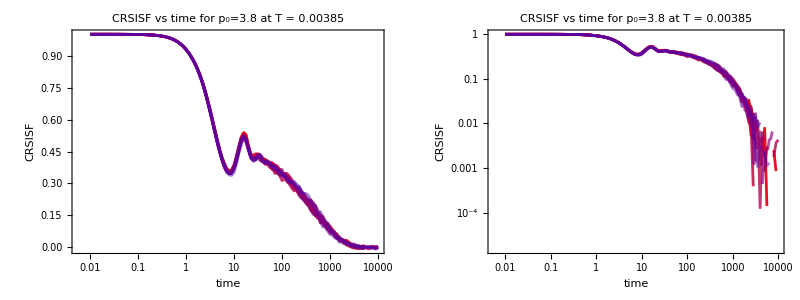

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>70&)][[1,1]],{i,10}]
```

{68,68,68,68,68,97,97,68,68,68}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,{99,100,98,98,99,145,142,100,99,101}[[i]]+5,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.00506467,0.00996245,0.00949554,0.0118561,0.00803932,0.00752896,0.0102121,0.0113782,0.00724978,0.00586607}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{101,100,98,97,99,145,142,100,99,103}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{641,641,641,641,641,641,639,640,640,641}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=1000.;
betaConstraints[[curP,curT]]={1.0>β>0.5,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.43>G>0.35,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.429995,0.429996,0.429998,0.429994,0.428011,0.429995,0.42999,0.421334,0.429996,0.429909}

0.42890.0027

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{550.172,532.959,512.017,608.635,520.313,518.11,556.325,590.286,485.29,627.467}

550.46.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.772807,0.777637,0.818004,0.789505,0.782125,0.781333,0.854232,0.851609,0.859687,0.843627}

0.810.04

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
""
```

### T=0.005

```mathematica
curP=3;curT=9;
```

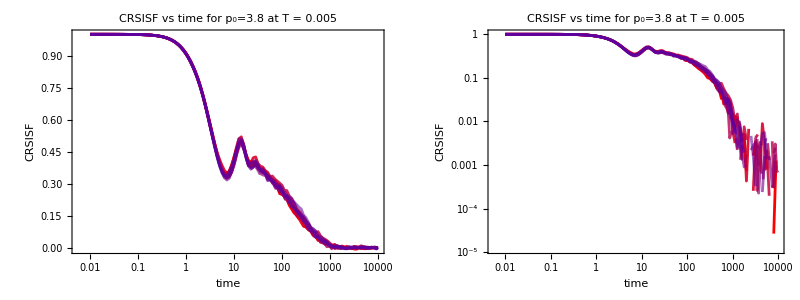

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>50&)][[1,1]],{i,10}]
```

{65,65,65,65,92,92,92,65,65,65}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,{91,94,90,93,128,131,131,90,91,91}[[i]]+5,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.00832382,0.00735019,0.0101993,0.00758862,0.00865569,0.00831836,0.00752716,0.00710162,0.00828622,0.0090828}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{91,94,90,93,128,131,131,90,91,91}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,161,161,161,111,111,111}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=1000.;
betaConstraints[[curP,curT]]={1.0>β>0.5,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.45>G>0.35,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.449988,0.44998,0.449986,0.449984,0.449948,0.438992,0.431882,0.435076,0.378943,0.449915}

0.4380.022

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{191.657,194.119,221.281,244.567,198.412,221.268,216.414,245.559,308.942,208.888}

225.35.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.846752,0.860496,0.850036,0.856563,0.814787,0.876278,0.835078,0.838594,0.999914,0.819439}

0.860.05

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.0063

```mathematica
curP=3;curT=8;
```

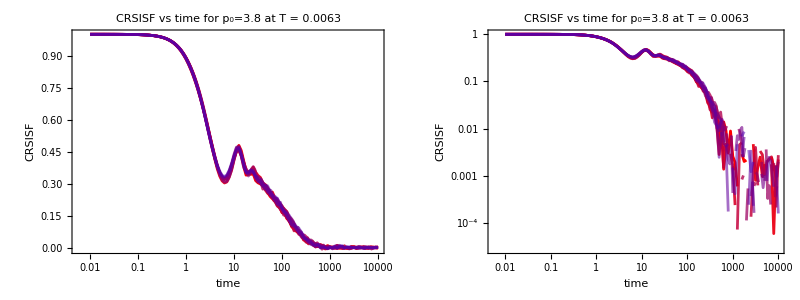

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>40&)][[1,1]],{i,10}]
```

{64,64,64,64,90,90,64,90,64,64}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,{85,84,84,85,124,123,86,125,84,84}[[i]]+5,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.0102407,0.00793322,0.00983405,0.0087889,0.00759445,0.00877181,0.0109633,0.0104207,0.00831714,0.0105694}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{85,84,84,85,124,123,83,125,84,84}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,161,161,161,111,111,111}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=1000.;
betaConstraints[[curP,curT]]={1.0>β>0.5,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.52>G>0.42,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.450535,0.420031,0.420246,0.435265,0.519965,0.420133,0.42007,0.493506,0.420048,0.433325}

0.4430.035

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{102.636,128.176,112.149,108.726,88.664,129.419,122.858,99.0334,117.454,127.902}

114.14.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.839529,0.981245,0.916907,0.884636,0.70368,0.865808,0.944656,0.790393,0.897675,0.891102}

0.870.08

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.008

```mathematica
curP=3;curT=7;
```

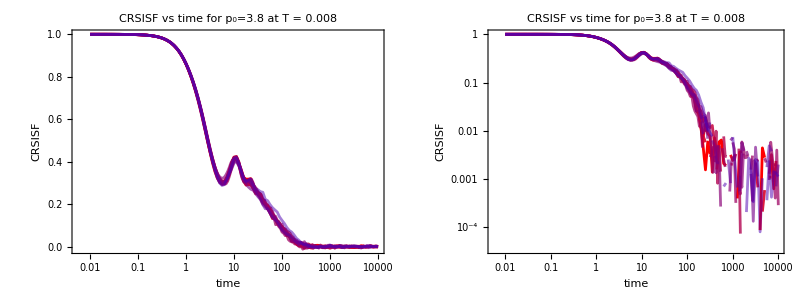

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>30&)][[1,1]],{i,10}]
```

{61,61,61,61,86,86,86,61,61,61}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,{77,77,77,82,114,110,115,79,77,80}[[i]]+5,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.00920302,0.00804024,0.0089202,0.00716326,0.0095515,0.0101005,0.00875587,0.010573,0.00797336,0.00755665}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{77,77,77,82,114,110,116,79,81,82}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,161,161,161,111,111,111}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=1000.;
betaConstraints[[curP,curT]]={1.0>β>0.5,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.45>G>0.4,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.408716,0.411213,0.4499,0.449963,0.449857,0.449955,0.449941,0.401098,0.449897,0.400107}

0.4320.023

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{64.1912,63.0843,56.4488,56.5898,61.1332,55.3384,60.7382,61.2782,52.8481,84.1045}

62.9.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.999835,0.919303,0.818529,0.79882,0.832561,0.999749,0.745222,0.932014,0.728128,0.958198}

0.870.10

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.01

```mathematica
curP=3;curT=6;
```

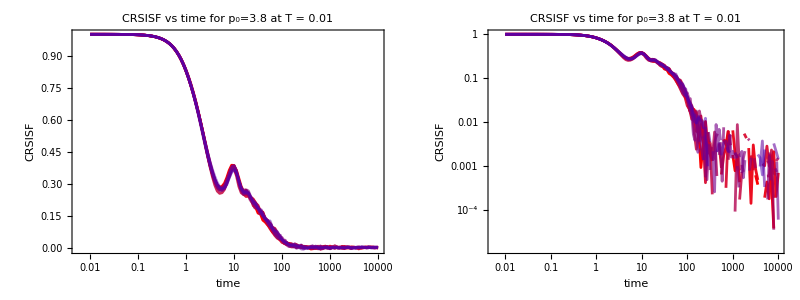

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>30&)][[1,1]],{i,10}]
```

{61,61,61,61,61,86,86,86,61,61}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,{74,75,72,73,72,104,103,103,73,74}[[i]]+5,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.0093895,0.00799356,0.0112076,0.00913944,0.00935345,0.0132575,0.00836863,0.0088405,0.00884129,0.00906708}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{75,75,74,73,76,104,107,104,76,77}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,161,161,161,111,111,111}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=1000.;
betaConstraints[[curP,curT]]={1.0>β>0.5,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.46>G>0.4,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.454702,0.400427,0.457578,0.417982,0.410566,0.400215,0.459577,0.400101,0.44431,0.400226}

0.4250.026

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{31.14,43.0099,34.1383,41.1859,39.9446,40.3674,35.8011,42.4467,36.2677,42.7685}

39.4.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.830519,0.998017,0.995247,0.933647,0.999616,0.924148,0.89011,0.967711,0.993935,0.942149}

0.950.06

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.016

```mathematica
curP=3;curT=5;
```

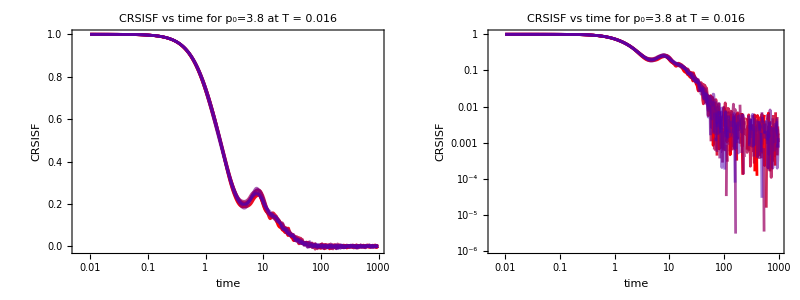

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>18&)][[1,1]],{i,10}]
```

{207,207,207,207,207,207,207,207,207,207}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,270,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.00998992,0.0109972,0.00947485,0.0110687,0.012008,0.011986,0.0104412,0.0108483,0.0114313,0.00990008}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{259,256,251,252,251,254,257,251,251,250}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,161,161,161,111,111,111}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=1000.;
betaConstraints[[curP,curT]]={1.0>β>0.5,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.46>G>0.4,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.459081,0.401343,0.417643,0.459655,0.459044,0.400199,0.459698,0.459803,0.459574,0.459159}

0.4440.026

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{10.3804,15.0829,14.6202,12.1786,13.8625,15.8662,12.4525,13.8849,12.4334,12.5059}

13.31.6

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.789962,0.956428,0.914257,0.760899,0.941127,0.997426,0.839778,0.999826,0.866619,0.890336}

0.900.08

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.025

```mathematica
curP=3;curT=4;
```

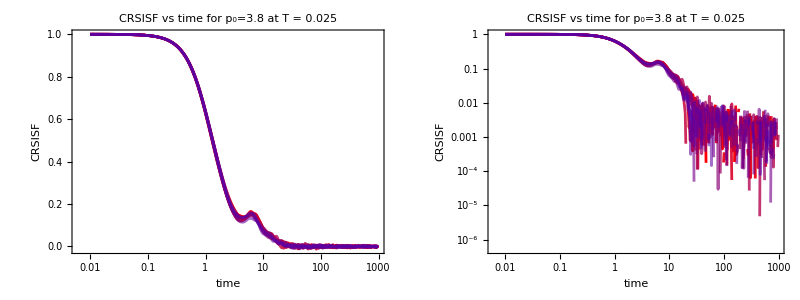

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>8&)][[1,1]],{i,10}]
```

{172,172,172,172,172,172,172,172,172,172}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,220,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.0134161,0.00985002,0.0116966,0.0110073,0.0140363,0.0132887,0.00989069,0.0124724,0.00956695,0.0111628}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{224,214,222,207,221,216,215,214,214,215}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,161,161,161,111,111,111}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=1000.;
betaConstraints[[curP,curT]]={1.0>β>0.5,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.46>G>0.4,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.459915,0.459938,0.459844,0.459981,0.459672,0.459334,0.455059,0.459827,0.45961,0.424227}

0.4560.011

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{5.65312,6.2107,5.69378,5.91496,5.36755,5.52508,4.60823,5.44272,4.87213,6.03418}

5.50.5

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.789962,0.956428,0.914257,0.760899,0.941127,0.997426,0.839778,0.999826,0.866619,0.890336}

0.900.08

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.03105

```mathematica
curP=3;curT=3;
```

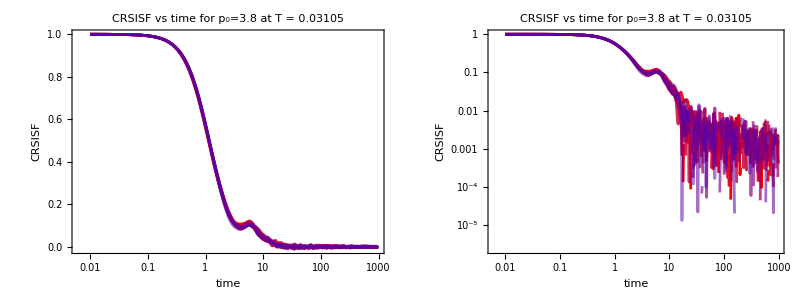

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>7&)][[1,1]],{i,10}]
```

{166,166,166,166,166,166,166,166,166,166}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,220,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.00909707,0.00938977,0.00902878,0.0100257,0.0102255,0.0101179,0.0105463,0.0101668,0.00960847,0.00845294}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{199,218,204,194,202,205,203,204,201,202}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,161,161,161,111,111,111}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=1000.;
betaConstraints[[curP,curT]]={1.0>β>0.5,1.0>β>0.5,1.0>β>0.999,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.999,1.0>β>0.999};
plateauConstraints[[curP,curT]]={0.5>G>0.4,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,i]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.499912,0.499769,0.409239,0.498606,0.409005,0.499281,0.499236,0.494133,0.475362,0.474879}

0.480.04

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{4.05079,3.7343,4.24275,4.11566,3.9403,3.78714,3.18954,4.02725,4.01448,4.16728}

3.930.30

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.999904,0.772629,0.999276,0.998107,0.809607,0.83622,0.74351,0.853858,0.999296,0.999242}

0.900.11

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.039

```mathematica
curP=3;curT=2;
```

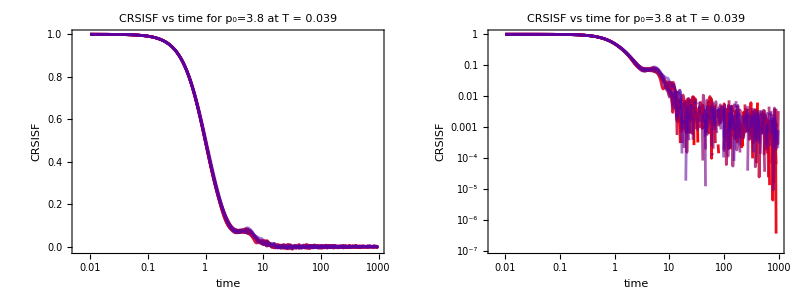

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>6&)][[1,1]],{i,10}]
```

{159,159,159,159,159,159,159,159,159,159}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,200,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.00880247,0.00851974,0.0102037,0.00990364,0.00943714,0.00998297,0.00952485,0.00954082,0.00886855,0.0100198}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{195,193,184,192,193,180,187,185,200,192}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,161,161,161,111,111,111}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=1000.;
betaConstraints[[curP,curT]]={1.0>β>0.8,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.5>G>0.4,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.498923,0.40017,0.415021,0.499405,0.498873,0.499489,0.499873,0.497694,0.499895,0.465828}

0.480.04

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{2.86841,2.67888,2.26229,2.75284,2.45638,2.77583,2.95268,3.06805,3.0134,2.81932}

2.760.25

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.986511,0.80011,0.800769,0.889447,0.801649,0.999667,0.999904,0.999418,0.999899,0.801118}

0.910.10

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.063

```mathematica
curP=3;curT=1;
```

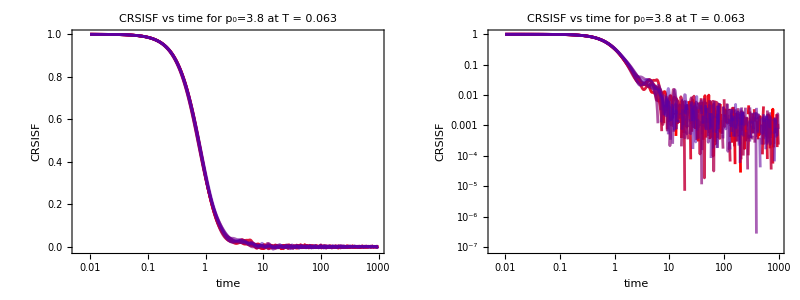

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>1&)][[1,1]],{i,10}]
```

{82,82,82,82,82,82,82,82,82,82}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,200,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <5*10^-2&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{113,117,115,115,119,112,115,117,115,120}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,161,161,161,111,111,111}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=1000.;
betaConstraints[[curP,curT]]={1.0>β>0.5,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={1.0>G>0.4,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.999996,0.999995,0.999996,0.999996,0.99999,0.999997,0.999995,0.99999,0.999996,0.999995}

0.999994626

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.80086,0.798091,0.792575,0.816617,0.823598,0.793925,0.808113,0.819445,0.821588,0.848777}

0.8120.017

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.999998,0.999997,0.999998,0.999998,0.999994,0.999998,0.999997,0.999991,0.999998,0.999997}

0.999996624

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],10}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### Summary

#### fitting results

```mathematica
fittings[[curP]]
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

```mathematica
fittings[[3]]={{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}};
```

#### fitting parameter

```mathematica
curP=3
```

3

```mathematica
Table[Dimensions[fittings[[curP,i]]],{i,11}]
```

{{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10}}

```mathematica
fittings[[curP,4]]
```

{}

```mathematica
tauAlphaResults[[curP]]=Table[Around[Mean[Table[fittings[[curP,T,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,T]]]}]],StandardDeviation[Table[fittings[[curP,T,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,T]]]}]]],{T,Length[temperatures[[curP]]]}]
```

{0.8120.017,2.760.25,3.930.30,5.50.5,13.31.6,39.4.,62.9.,114.14.,225.35.,550.46.,1423.279.,2572.497.,4591.765.,8.31.210^3}

```mathematica
plateauResults[[curP]]=Table[Around[Mean[Table[fittings[[curP,T,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,T]]]}]],StandardDeviation[Table[fittings[[curP,T,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,T]]]}]]],{T,Length[temperatures[[curP]]]}]
```

{0.999994713,0.480.04,0.480.04,0.4560.011,0.4440.026,0.4250.026,0.4320.023,0.4430.035,0.4710.023,0.4430.011,0.4540.022,0.4250.024,0.4340.008,0.4440.016}

```mathematica
betaResults[[curP]]=Join[Table[Around[Mean[Table[fittings[[curP,T,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,T]]]}]],StandardDeviation[Table[fittings[[curP,T,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,T]]]}]]],{T,Length[temperatures[[curP]]]}]]
```

{0.99999698,0.910.10,0.900.11,0.910.09,0.900.09,0.940.05,0.920.06,0.870.08,0.7860.028,0.810.04,0.810.12,0.920.09,0.920.08,0.860.14}

```mathematica
numExp[[curP]]=Table[Count[Table[fittings[[curP,T,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,T]]]}],_?(#>0.99&)],{T,Length[temperatures[[curP]]]}]
```

{10,4,5,4,3,2,2,0,0,0,1,4,3,3}

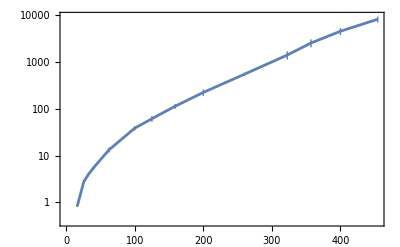

```mathematica
ListLogPlot[Table[{1/temperatures[[curP,T]],tauAlphaResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],Joined->True]
```

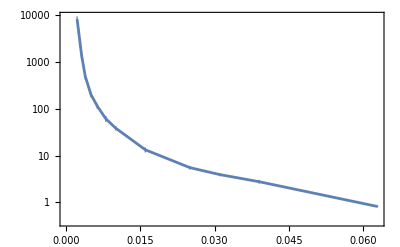

```mathematica
ListLogPlot[Table[{temperatures[[curP,T]],tauAlphaResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],Joined->True]
```

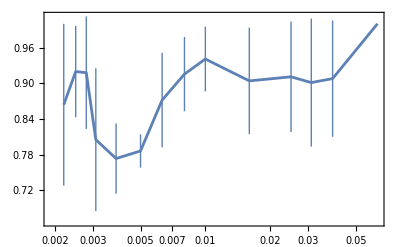

```mathematica
ListLogLinearPlot[Table[{temperatures[[curP,T]],betaResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],Joined->True]
```

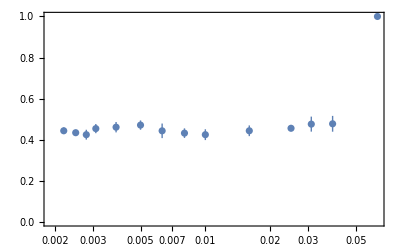

```mathematica
ListLogLinearPlot[Table[{temperatures[[curP,T]],plateauResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],PlotRange->All]
```

## p_0=3.75

### T=0.0093

```mathematica
curP=4;curT=11;
```

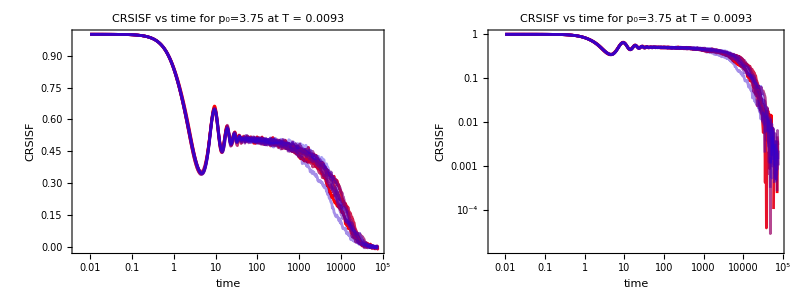

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>200&)][[1,1]],{i,10}]
```

{312,312,312,312,312,312,312,312,312,312}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,550,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.0156649,0.0105761,0.00894927,0.00845761,0.0119465,0.0117239,0.00864053,0.0101218,0.00639035,0.0103232}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{527,529,535,536,542,541,536,532,534,542}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{569,569,568,569,569,569,569,568,569,568}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=10000.;
betaConstraints[[curP,curT]]={1.0>β>0.5,0.74>β>0.70,0.78>β>0.72,0.74>β>0.70,0.78>β>0.70,0.78>β>0.72,0.78>β>0.71,0.78>β>0.73,0.78>β>0.71,0.78>β>0.72};
plateauConstraints[[curP,curT]]={0.9>G>0.3,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.497781,0.500201,0.504398,0.493927,0.511512,0.497498,0.507981,0.517032,0.509922,0.52152}

0.5060.009

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{9044.44,12589.9,12742.3,9528.82,11420.2,13541.4,10094.5,9773.65,6473.87,11735.7}

1.070.2110^4

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.961335,0.999999,0.999996,0.99998,0.947139,0.999999,0.960629,0.999999,0.923303,0.999999}

0.9790.029

```mathematica
0.75
```

0.75

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.01

```mathematica
curP=4;curT=10;
```

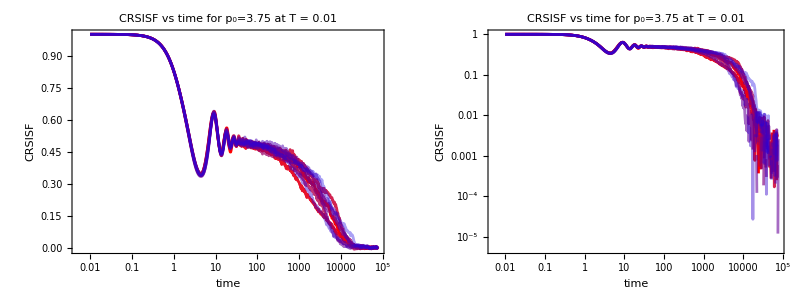

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>70&)][[1,1]],{i,10}]
```

{266,266,266,266,266,266,266,266,266,266}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,530,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.00775574,0.0101563,0.00755071,0.00888165,0.00763267,0.0085646,0.0068896,0.0113681,0.0084356,0.0117008}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{513,505,508,494,514,508,486,511,493,515}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{568,569,567,568,568,569,569,569,569,568}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=8000.;
betaConstraints[[curP,curT]]={1.0>β>0.8,1.0>β>0.5,1.0>β>0.9999,1.0>β>0.9999,1.0>β>0.9999,1.0>β>0.9999,1.0>β>0.9999,1.0>β>0.9999,1.0>β>0.9999,1.0>β>0.9999};
plateauConstraints[[curP,curT]]={0.52>G>0.3,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38,0.405>G>0.39,0.405>G>0.39,0.405>G>0.39,0.42>G>0.38};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.494272,0.491547,0.488649,0.504164,0.473651,0.511137,0.498641,0.499682,0.512123,0.482533}

0.4960.012

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{4497.3,2832.32,6626.76,3386.37,5442.21,4553.6,4083.79,5968.89,2751.11,7014.45}

4.71.510^3

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.86655,0.672499,0.913901,0.86169,0.8183,0.818991,0.999999,0.911416,0.841402,0.841428}

0.850.08

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.011

```mathematica
curP=4;curT=9;
```

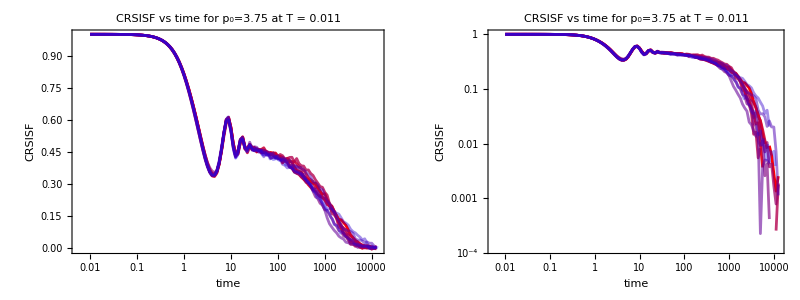

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>60&)][[1,1]],{i,10}]
```

{67,67,67,67,67,67,67,67,67,95}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <10^-2&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{106,104,107,103,106,104,104,111,109,152}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{113,113,113,113,113,113,113,113,113,165}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=8000.;
betaConstraints[[curP,curT]]={1.0>β>0.0999,1.0>β>0.5,1.0>β>0.999,1.0>β>0.999,1.0>β>0.5,1.0>β>0.999,1.0>β>0.999,1.0>β>0.999,1.0>β>0.5,1.0>β>0.999};
plateauConstraints[[curP,curT]]={0.9>G>0.44,1.0>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.478528,0.479729,0.475176,0.474676,0.464739,0.482873,0.468318,0.466061,0.527937,0.461735}

0.4780.019

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{1498.75,1255.04,1457.95,1453.47,1358.19,1048.01,1001.07,1593.17,1215.15,1147.19}

1303.201.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.79439,0.775997,0.889056,0.999996,0.822386,0.883042,0.999985,0.876531,0.554483,0.906506}

0.850.13

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
""
```

### T=0.012

```mathematica
curP=4;curT=8;
```

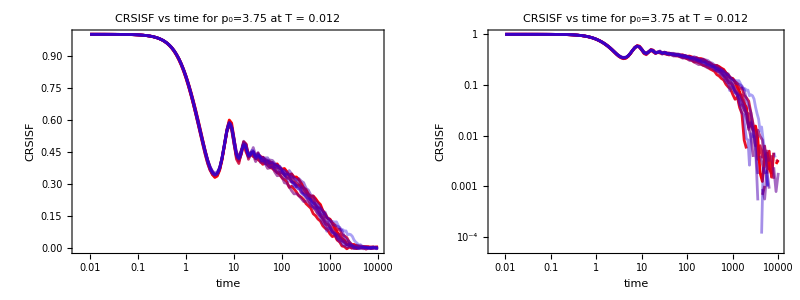

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>50&)][[1,1]],{i,10}]
```

{65,65,65,65,65,65,65,65,92,92}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <0.5*10^-2&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{102,97,101,99,104,99,101,101,141,152}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{569,569,568,569,569,569,569,568,569,568}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=800.;
betaConstraints[[curP,curT]]={1.0>β>0.7,1.0>β>0.5,1.0>β>0.5,1.0>β>0.999,1.0>β>0.5,1.0>β>0.5,1.0>β>0.999,1.0>β>0.5,1.0>β>0.999,1.0>β>0.5};
plateauConstraints[[curP,curT]]={0.5>G>0.3,1.0>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.432828,0.467265,0.444219,0.448966,0.478672,0.443697,0.457452,0.451933,0.467008,0.430604}

0.4520.016

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{773.949,414.329,725.584,608.992,496.054,527.329,609.034,767.406,502.278,798.075}

622.137.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.927947,0.755369,0.730546,0.834492,0.761655,0.700037,0.881504,0.816403,0.834545,0.700004}

0.790.08

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.014

```mathematica
curP=4;curT=7;
```

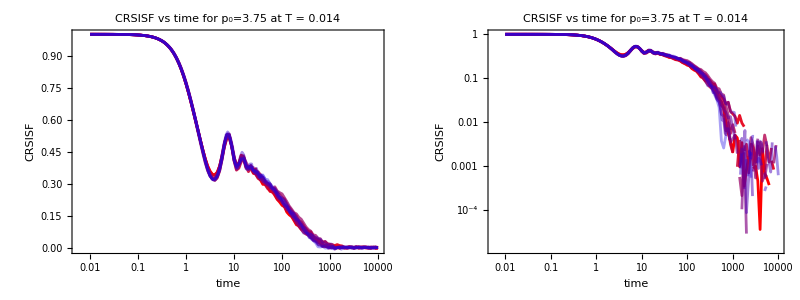

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>40&)][[1,1]],{i,10}]
```

{64,64,64,64,64,64,64,90,90,64}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,{87,92,87,88,89,87,90,125,132,85}[[i]]+5,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.006283,0.00532394,0.00603922,0.00770921,0.00555474,0.00666217,0.00627655,0.00721614,0.00891495,0.00788575}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{88,96,89,89,90,87,91,125,132,85}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,111,111,111,161,161,111}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=200.;
betaConstraints[[curP,curT]]={1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.999,1.0>β>0.999,1.0>β>0.999,1.0>β>0.999,1.0>β>0.5,1.0>β>0.999};
plateauConstraints[[curP,curT]]={0.42>G>0.3,1.0>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.419982,0.419992,0.410141,0.399947,0.407883,0.412849,0.402384,0.419914,0.419995,0.419988}

0.4130.008

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{148.507,171.475,157.363,198.609,212.758,170.578,186.64,164.63,177.929,163.575}

175.19.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.799444,0.772417,0.85095,0.894927,0.854409,0.890404,0.894819,0.882715,0.81313,0.999895}

0.870.06

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.016

```mathematica
curP=4;curT=6;
```

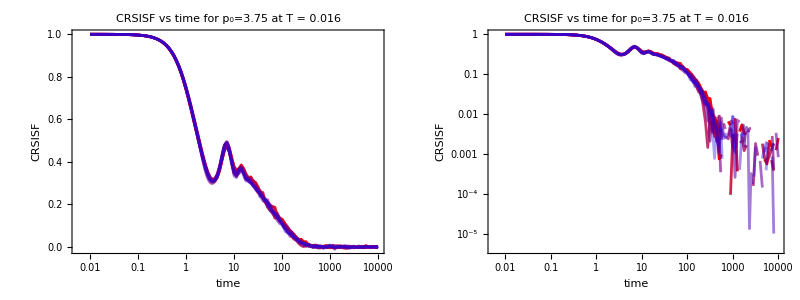

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>30&)][[1,1]],{i,10}]
```

{61,61,61,61,61,86,61,86,61,86}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,{81,82,80,78,81,115,79,116,81,115}[[i]]+5,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.00926954,0.0076386,0.00811699,0.00865967,0.00875467,0.0100119,0.0106033,0.00848336,0.0089282,0.00833925}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{82,82,80,78,81,115,79,118,82,117}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,111,161,111,161,111,161}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=200.;
betaConstraints[[curP,curT]]={1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.999,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5};
plateauConstraints[[curP,curT]]={0.48>G>0.44,1.0>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,i]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.479845,0.448319,0.479881,0.440006,0.440051,0.440164,0.479779,0.479942,0.443579,0.478301}

0.4610.020

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{62.8449,73.6809,57.8897,69.5328,72.3414,70.306,56.3544,59.6555,67.7179,60.2015}

65.6.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.716578,0.82785,0.742063,0.999012,0.830836,0.863061,0.771295,0.8139,0.826693,0.787078}

0.820.08

```mathematica
0.780.16
```

0.780.16

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.02

```mathematica
curP=4;curT=5;
```

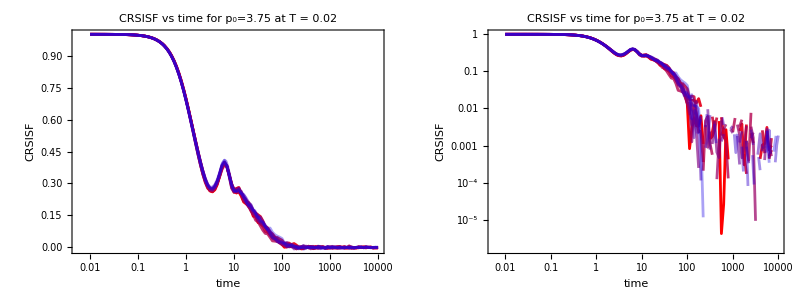

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>16&)][[1,1]],{i,10}]
```

{56,56,56,56,56,56,56,56,78,56}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,{71,77,74,71,72,71,75,72,103,75}[[i]]+5,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.0082055,0.00768341,0.0074413,0.00947869,0.00821376,0.00739847,0.00783995,0.00786849,0.00766395,0.009395}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{71,77,74,71,72,72,75,73,103,76}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,111,111,111,161,161,111}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=80.;
betaConstraints[[curP,curT]]={1.0>β>0.5,1.0>β>0.999,1.0>β>0.999,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.999,1.0>β>0.5,1.0>β>0.999,1.0>β>0.5,1.0>β>0.999};
plateauConstraints[[curP,curT]]={0.6>G>0.3,1.0>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.498218,0.387643,0.599875,0.599643,0.382933,0.414158,0.599273,0.447245,0.401183,0.402486}

0.470.09

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{20.8707,33.268,16.3588,16.6402,30.985,27.9242,18.2839,28.2634,30.4113,31.6073}

25.7.

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.738386,0.93051,0.64727,0.766249,0.998581,0.881412,0.69797,0.842817,0.939038,0.781587}

0.820.11

```mathematica
0.780.16
```

0.780.16

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],300}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.025

```mathematica
curP=4;curT=4;
```

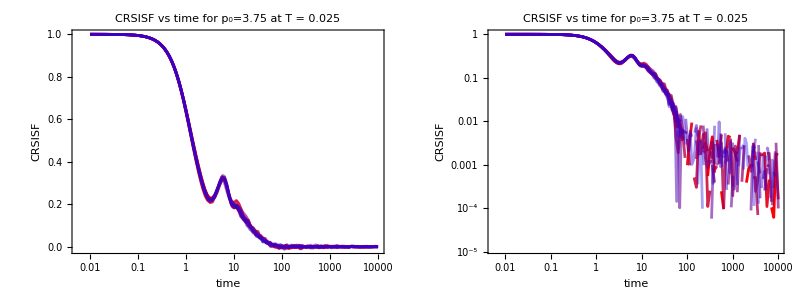

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>15&)][[1,1]],{i,10}]
```

{55,55,55,55,55,55,77,77,77,77}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,{66,65,66,65,66,66,93,93,95,94}[[i]]+5,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.00712468,0.0078402,0.00705519,0.0097944,0.00751414,0.00748483,0.00806703,0.0100175,0.00908577,0.00759967}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{67,65,67,65,68,68,95,93,95,94}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,111,111,161,161,161,161}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=80.;
betaConstraints[[curP,curT]]={1.0>β>0.5,1.0>β>0.999,1.0>β>0.999,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.999,1.0>β>0.5,1.0>β>0.999,1.0>β>0.5,1.0>β>0.999};
plateauConstraints[[curP,curT]]={0.5>G>0.4,1.0>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.40239,0.401329,0.402386,0.403409,0.401685,0.499485,0.499301,0.400429,0.498425,0.492527}

0.440.05

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{14.7879,14.2608,15.7008,13.8567,13.68,13.2937,10.4577,15.0652,10.6998,11.4316}

13.31.8

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.907865,0.824088,0.997179,0.805891,0.783168,0.863968,0.787307,0.963972,0.743065,0.810176}

0.850.08

```mathematica
0.780.16
```

0.780.16

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],300}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.03105

```mathematica
curP=4;curT=3;
```

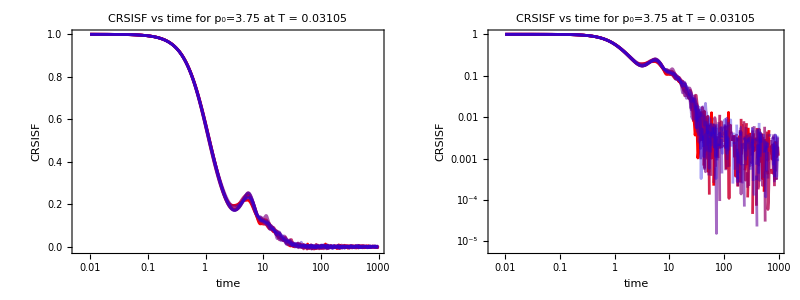

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>15&)][[1,1]],{i,10}]
```

{199,199,199,199,199,199,199,199,199,199}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,235,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.0106733,0.0116966,0.0126606,0.0129797,0.0115945,0.0114976,0.0106605,0.00946916,0.0153248,0.0108576}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{225,223,227,235,232,232,228,223,230,230}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,111,111,161,161,161,161}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=5.;
betaConstraints[[curP,curT]]={1.0>β>0.5,1.0>β>0.999,1.0>β>0.999,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.999,1.0>β>0.5,1.0>β>0.999,1.0>β>0.5,1.0>β>0.999};
plateauConstraints[[curP,curT]]={0.5>G>0.4,1.0>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.40915,0.410288,0.498266,0.498886,0.49953,0.400982,0.498709,0.499874,0.400506,0.409296}

0.450.05

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{8.66153,8.69725,7.06172,7.92001,7.8435,9.26457,7.06425,8.09225,9.74042,7.95354}

8.20.9

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.980294,0.996811,0.869104,0.853964,0.973386,0.898793,0.89726,0.999901,0.984751,0.81955}

0.930.07

```mathematica
0.780.16
```

0.780.16

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],300}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.039

```mathematica
curP=4;curT=2;
```

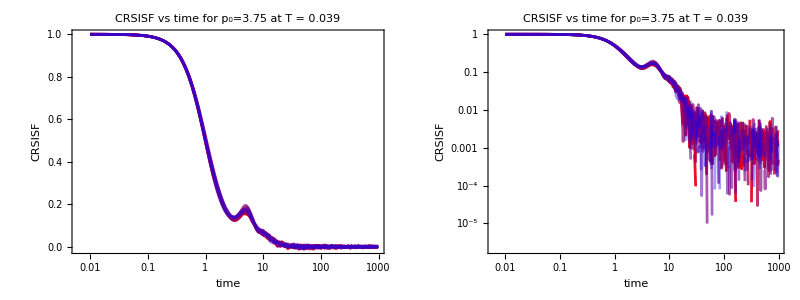

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>6&)][[1,1]],{i,10}]
```

{159,159,159,159,159,159,159,159,159,159}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,230,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.0101019,0.0102193,0.00948621,0.0100223,0.00974036,0.010759,0.00859665,0.0116157,0.00842739,0.0100414}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{221,203,217,218,203,207,216,215,214,208}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,111,111,161,161,161,161}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=5.;
betaConstraints[[curP,curT]]={1.0>β>0.7,1.0>β>0.999,1.0>β>0.999,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.999,1.0>β>0.5,1.0>β>0.999,1.0>β>0.5,1.0>β>0.999};
plateauConstraints[[curP,curT]]={0.5>G>0.43,1.0>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.499833,0.499931,0.499832,0.49981,0.499912,0.499887,0.499904,0.499759,0.499916,0.432874}

0.4930.021

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{3.93425,4.36442,3.89567,4.1742,4.45253,4.1118,4.63237,3.8654,4.33187,5.11292}

4.30.4

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.757649,0.915274,0.770849,0.774875,0.892236,0.834116,0.887193,0.73613,0.891394,0.981729}

0.840.08

```mathematica
0.780.16
```

0.780.16

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],300}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### T=0.063

```mathematica
curP=4;curT=1;
```

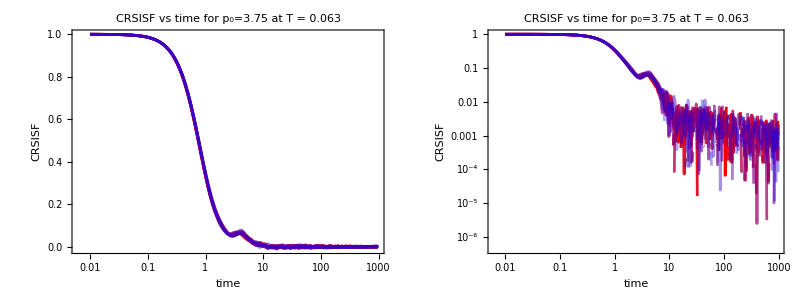

```mathematica
Grid[Partition[{ListLogLinearPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True],ListLogLogPlot[Table[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],{i,10}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],FrameLabel->{"time","CRSISF"},ImageSize->400,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[curP]]]<>" at T = "<>ToString[temperatures[[curP,curT]]],Joined->True]},2]]
```

```mathematica
fitStartPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,1]]]-CRSISF[[curP,curT,i,1,1]],_?(#>4&)][[1,1]],{i,10}]
```

{142,142,142,142,142,142,142,142,142,142}

```mathematica
noiseLevel[[curP,curT]]=Table[3*StandardDeviation[Table[CRSISF[[curP,curT,i,2,time]],{time,185,Length[CRSISF[[curP,curT,i,2]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

{0.00796349,0.00852588,0.00867794,0.0084953,0.00857468,0.00882804,0.00883867,0.0110249,0.0093079,0.00983803}

```mathematica
fitEndPos[[curP,curT]]=Table[Position[Normal[CRSISF[[curP,curT,i,2]]],_?(# <noiseLevel[[curP,curT,i]]&)][[1,1]]-1,{i,Length[CRSISF[[curP,curT]]]}]
```

{172,173,179,181,173,166,176,178,167,170}

```mathematica
fitEndPos[[curP,curT]]=Table[Length[CRSISF[[curP,curT,i,1]]],{i,Length[CRSISF[[curP,curT]]]}]
```

{111,111,111,111,111,111,161,161,161,161}

```mathematica
initialPlateau[[curP,curT]]=0.5;
initialBeta[[curP,curT]]=0.75;
initialTau[[curP,curT]]=1.;
betaConstraints[[curP,curT]]={1.0>β>0.5,1.0>β>0.999,1.0>β>0.999,1.0>β>0.5,1.0>β>0.5,1.0>β>0.5,1.0>β>0.999,1.0>β>0.5,1.0>β>0.999,1.0>β>0.5,1.0>β>0.999};
plateauConstraints[[curP,curT]]={0.5>G>0.43,1.0>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3,0.9>G>0.3};
tauConstraints[[curP,curT]]=0.9>G>0.1;
```

```mathematica
fittings[[curP,curT]]=Table[NonlinearModelFit[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,fitStartPos[[curP,curT,i]],fitEndPos[[curP,curT,i]]}],{stretchedExp[t,G,τ,β],{betaConstraints[[curP,curT,1]],plateauConstraints[[curP,curT,1]],20000>τ>0.5}},{{G,initialPlateau[[curP,curT]]},{τ,initialTau[[curP,curT]]},{β,initialBeta[[curP,curT]]}},t],{i,Length[CRSISF[[curP,curT]]]}]
```

{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.496728,0.430654,0.498817,0.499372,0.430912,0.499935,0.431296,0.497735,0.431573,0.499864}

0.4720.035

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{1.73903,2.25265,1.50522,2.02124,2.16412,2.20385,2.00497,1.42329,1.74074,2.2078}

1.930.30

```mathematica
Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]
Around[Mean[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]],StandardDeviation[Table[fittings[[curP,curT,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,curT]]]}]]]
```

{0.872737,0.965733,0.753946,0.999843,0.998082,0.999921,0.861233,0.697971,0.769987,0.999903}

0.890.12

```mathematica
0.780.16
```

0.780.16

```mathematica
Table[Show[ListLogLogPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLogPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,1,Length[CRSISF[[curP,curT,i,1]]]]]}]],{i,Length[CRSISF[[curP,curT]]]}]
```

```mathematica
Table[Show[ListLogLinearPlot[Table[{CRSISF[[curP,curT,i,1,rec]]-CRSISF[[curP,curT,i,1,1]],CRSISF[[curP,curT,i,2,rec]]},{rec,Length[CRSISF[[curP,curT,i,1]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[curP]]]],Joined->True],LogLinearPlot[fittings[[curP,curT,i]][x],{x,CRSISF[[curP,curT,i,1,fitStartPos[[curP,curT,i]]]]-CRSISF[[curP,curT,i,1,1]],100}]],{i,Length[CRSISF[[curP,curT]]]}]
```

### Summary

#### fitting results

```mathematica
fittings[[curP]]
```

{{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]},{FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…],FittedModel[…]}}

#### fitting parameter

```mathematica
curP=4
```

4

```mathematica
numExp[[curP]]=Table[Count[Table[fittings[[curP,T,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,T]]]}],_?(#>0.97&)],{T,Length[temperatures[[curP]]]}]
```

{3,0,5,1,1,1,1,0,2,1,6}

```mathematica
Table[Dimensions[fittings[[curP,i]]],{i,11}]
```

{{10},{10},{10},{10},{10},{10},{10},{10},{10},{10},{10}}

```mathematica
fittings[[curP,4]]
```

{}

```mathematica
tauAlphaResults[[curP]]=Table[Around[Mean[Table[fittings[[curP,T,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,T]]]}]],StandardDeviation[Table[fittings[[curP,T,i]]["BestFitParameters"][[2,2]],{i,Length[CRSISF[[curP,T]]]}]]],{T,Length[temperatures[[curP]]]}]
```

{1.930.30,4.30.4,8.20.9,13.31.8,25.7.,65.6.,175.19.,622.137.,1311.198.,4.71.510^3,1.070.2110^4}

```mathematica
plateauResults[[curP]]=Table[Around[Mean[Table[fittings[[curP,T,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,T]]]}]],StandardDeviation[Table[fittings[[curP,T,i]]["BestFitParameters"][[1,2]],{i,Length[CRSISF[[curP,T]]]}]]],{T,Length[temperatures[[curP]]]}]
```

{0.4720.035,0.4930.021,0.450.05,0.440.05,0.470.09,0.4610.020,0.4130.008,0.4520.016,0.4750.014,0.4960.012,0.5060.009}

```mathematica
betaResults[[curP]]=Join[Table[Around[Mean[Table[fittings[[curP,T,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,T]]]}]],StandardDeviation[Table[fittings[[curP,T,i]]["BestFitParameters"][[3,2]],{i,Length[CRSISF[[curP,T]]]}]]],{T,Length[temperatures[[curP]]]}]]
```

{0.880.11,0.840.07,0.920.07,0.850.08,0.830.12,0.820.08,0.870.06,0.790.08,0.860.12,0.870.06,0.9790.029}

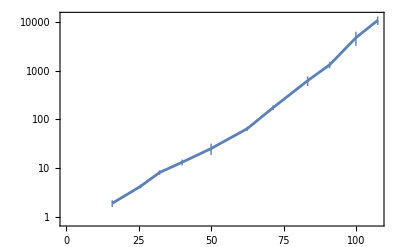

```mathematica
ListLogPlot[Table[{1/temperatures[[curP,T]],tauAlphaResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],Joined->True]
```

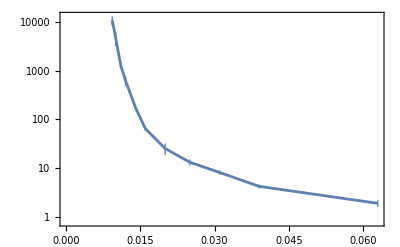

```mathematica
ListLogPlot[Table[{temperatures[[curP,T]],tauAlphaResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],Joined->True]
```

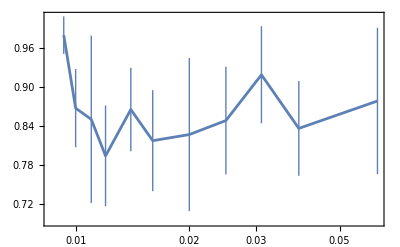

```mathematica
ListLogLinearPlot[Table[{temperatures[[curP,T]],betaResults[[curP,T]]},{T,Length[temperatures[[curP]]]}],Joined->True]
```

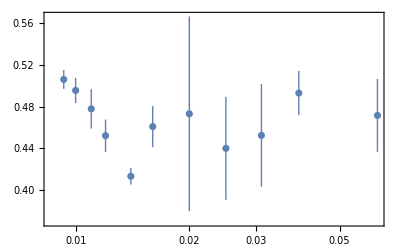

```mathematica
ListLogLinearPlot[Table[{temperatures[[curP,T]],plateauResults[[curP,T]]},{T,Length[temperatures[[curP]]]}]]
```